# KPR Specificity

No derivations will be provided in this document. For a complete documentation of the workflow, see KPR.nb

## Setup

```mathematica
expandParams={x->(c kon)/koff,g->koff/kf};
contractParams={c->koff/kon x,kf->koff/g};
cmap=ColorData[97,"ColorList"];
gradcolor={RGBColor[250/255,250/255,110/255],RGBColor[250/255,250/255,110/255],RGBColor[146/255,220/255,126/255],RGBColor[100/255,201/255,135/255],RGBColor[57/255,180/255,142/255],RGBColor[8/255,159/255,143/255],RGBColor[0/255,159/255,143/255],RGBColor[0/255,137/255,138/255],RGBColor[8/255,115/255,127/255],RGBColor[33/255,93/255,110/255],RGBColor[42/255,72/255,88/255]};

Pss0={koff/(koff+c kon),(c kon)/(koff+c kon)};
Pss1={koff/(koff+c kon),(c koff kon)/((kf+koff) (koff+c kon)),(c kf kon)/((kf+koff) (koff+c kon))};
Pss2={koff/(koff+c kon),(c koff kon)/((kf+koff) (koff+c kon)),(c kf koff kon)/((kf+koff)^2 (koff+c kon)),(c kf^2 kon)/((kf+koff)^2 (koff+c kon))};

μ0= kp t x/(1+x)/.expandParams;
μ1= (kp t)/(1+g)x/(1+x)/.expandParams;
μ2=(kp t)/(1+g)^2 x/(1+x)/.expandParams;
μ3=(kp t)/(1+g)^3 x/(1+x)/.expandParams;
μ4=(kp t)/(1+g)^4 x/(1+x)/.expandParams;
μN=(kp t)/(1+g)^Ns x/(1+x)/.expandParams;
```

```mathematica
(* All variances are given for large t *)
Σ0=(kp t x)/(1+x)+(2 kp^2 t x)/(koff(1+x)^3)/.expandParams;

Σ1=(kp t x ((1+g)^2 koff (1+x)^2+2 kp (1+g^2 (1+x)^2+g (2+x))))/((1+g)^3 koff (1+x)^3)/.expandParams;(*Limit of large t*)

Σ2=(kp t x ((1+g)^3 koff (1+x)^2+2 kp (1+3 g^2 (1+x)^2+g^3 (1+x)^2+g (3+2 x))))/((1+g)^5 koff (1+x)^3)/.expandParams;

Σ3=1/((1+g)^7 koff (1+x)^3)kp t x ((1+g)^4 koff (1+x)^2+2 kp (1+6 g^2 (1+x)^2+4 g^3 (1+x)^2+g^4 (1+x)^2+g (4+3 x)))/.expandParams;

Σ4=1/((1+g)^9 koff (1+x)^3)kp t x ((1+g)^5 koff (1+x)^2+2 kp (1+10 g^2 (1+x)^2+10 g^3 (1+x)^2+5 g^4 (1+x)^2+g^5 (1+x)^2+g (5+4 x)))/.expandParams;
```

```mathematica
ΣN=(kp t x ((1+g)^(Ns+1) koff (1+x)^2+2 kp ((1+g)^(Ns+1) (1+x)^2-x (2+x+g (2+Ns+Ns x+x)))))/((1+g)^(1+2Ns) koff (1+x)^3);
(* (kp t x)/((1+x)(1+g)^Ns)+((2 kp^2 t x)/((koff+koff x)(1+g)^Ns)-(2 kp^2 t x^2 (2+x+g (2+Ns+Ns x+x)))/((1+g)^(1+2Ns) koff (1+x)^3)) *)
```

```mathematica
η0=(Pss0[[2]]/.koff->δ koff)/Pss0[[2]];
η1=(Pss1[[3]]/.koff->δ koff)/Pss1[[3]];
η2=(Pss2[[4]]/.koff->δ koff)/Pss2[[4]];
ηN=((kf+koff)^Ns (koff+c kon))/((kf+koff δ)^Ns (c kon+koff δ));
```

```mathematica
BPMetric[mean_,var_]:=(mean-(mean/.koff->δ koff))^2/(var+(var/.koff->δ koff))
```

```mathematica
κ0estimator=(koff/.Solve[μ0==n/.expandParams,koff][[1]]);
κ1estimator=(koff/.Solve[μ1==n/.expandParams,koff][[1]]);
κ2estimator=(koff/.Solve[μ2==n/.expandParams,koff][[2]]);
κ3estimator=(koff/.Solve[μ3==n/.expandParams,koff][[1]]);
κ4estimator=(koff/.Solve[μ4==n/.expandParams,koff][[1]]);

κ0=κ0estimator/.n->μ0;
κ1=κ1estimator/.n->μ1;
κ2=κ2estimator/.n->μ2;
κ3=κ3estimator/.n->μ3;
κ4=κ4estimator/.n->μ4;


Σk0=Σ0/D[Evaluate[μ0/.expandParams],koff]^2//Simplify;
Σk1=Σ1/D[Evaluate[μ1/.expandParams],koff]^2//Simplify;
Σk2=Σ2/D[Evaluate[μ2/.expandParams],koff]^2//Simplify;
Σk3=Σ3/D[Evaluate[μ3/.expandParams],koff]^2//Simplify;
Σk4=Σ4/D[Evaluate[μ4/.expandParams],koff]^2//Simplify;
Σk5=(ΣN/.Ns->5)/D[Evaluate[μN/.Ns->5/.expandParams],koff]^2//Simplify;
Σk6=(ΣN/.Ns->6)/D[Evaluate[μN/.Ns->6/.expandParams],koff]^2//Simplify;

ΣkN=Evaluate[ΣN/.expandParams]/D[μN,koff]^2//Simplify;
```

```mathematica
Σk1/.contractParams//FullSimplify
```

((1+g) koff (1+x) ((1+g)^2 koff (1+x)^2+2 kp (1+g (2+x+g (1+x)^2))))/(kp t x (1+g (2+x))^2)

```mathematica
((1+g) (1+x) (((1+g) koff (1+x))^2+2 kp koff ((1+g(1+x))^2-g x)))/(kp t x (1+g (2+x))^2)
```

((1+g) (1+x) ((1+g)^2 koff^2 (1+x)^2+2 koff kp (-g x+(1+g (1+x))^2)))/(kp t x (1+g (2+x))^2)

```mathematica
(*κ1 = (-1/kf(1+g x)+√((1+g x)^2+4g))/2*)
```

```mathematica
xgParams={kon->1,kp->1,t->100,koff->10^gtest,δ->0.1,c->10^ctest,kf->1};
xgTicks={{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Table[{i,Superscript[10,i]},{i,-3,3}],None}};
gxTicks={{Table[{i,Superscript[10,i]},{i,-3,3}],None},{Table[{i,Superscript[10,i]},{i,-1,3}],None}};
```

```mathematica
SnR=μN/(√ΣN)/.expandParams;
SnRBP=κ1/(√Σk1);
KPR0BPn=BPMetric[μ0,Σ0];
KPR1BPn=BPMetric[μ1,Σ1];
KPR2BPn=BPMetric[μ2,Σ2];
KPR3BPn=BPMetric[μ3,Σ3];
KPR4BPn=BPMetric[μ4,Σ4];
KPR5BPn=BPMetric[Evaluate[μN/.Ns->5],Evaluate[ΣN/.Ns->5]];
KPRNBPn=BPMetric[μN,ΣN];

KPR0BPk=BPMetric[koff,Σk0];
KPR1BPk=BPMetric[koff,Σk1];
KPR2BPk=BPMetric[koff,Σk2];
KPR3BPk=BPMetric[koff,Σk3];
KPR4BPk=BPMetric[koff,Σk4];
KPR5BPk=BPMetric[koff,Σk5];
KPRNBPk=BPMetric[koff,ΣkN];
```

## Figures

```mathematica
m1=-0.5;
std1=0.5;
std2=1.25;
increment=2;
```

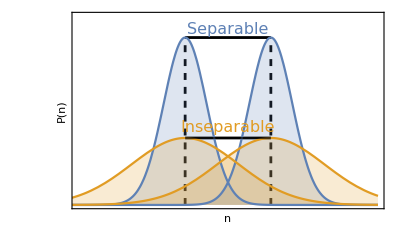

```mathematica
max1=Max[Table[PDF[NormalDistribution[m1,std1],x],{x,m1-0.1,m1+0.1,0.01}]];
max2=Max[Table[PDF[NormalDistribution[m1,std2],x],{x,m1-0.1,m1+0.1,0.01}]];
Fig1B=Show[
ListPlot[{Table[{m1,y},{y,0,1.05*max1,0.1}],Table[{m1+increment,y},{y,0,1.05*max1,0.1}],Table[{x,max1},{x,m1,m1+increment,0.1}],Table[{x,max2},{x,m1,m1+increment,0.1}]},

Joined->True,PlotStyle->{{Dashed,Black,Thickness[0.005]},{Dashed,Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]}},
Frame->{{True,False},{True,False}},FrameStyle->Black,LabelStyle->{Black,FontSize->24},FrameTicks->None,Axes->{True,False},PlotRange->{{-3,4},{0,0.9}},FrameLabel->{"n","P(n)"},

Epilog->{Line[{{m1,max1},{m1+increment,max1}}],Text[Style["Separable",cmap[[1]],FontSize->16],{m1+0.5*increment,1.05*max1}],
Line[{{m1,max2},{m1+increment,max2}}],Text[Style["Inseparable",cmap[[2]],FontSize->16],{m1+0.5*increment,1.15*max2}]
}],

Plot[{PDF[NormalDistribution[m1,std1],x],PDF[NormalDistribution[m1+increment,std1],x],PDF[NormalDistribution[m1,std2],x],PDF[NormalDistribution[m1+increment,std2],x]},{x,-4,4},
PlotStyle->{cmap[[1]],cmap[[1]],cmap[[2]],cmap[[2]]},
Filling->Axis]
]
```

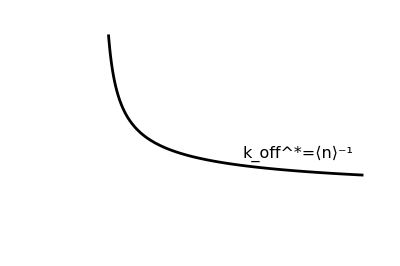
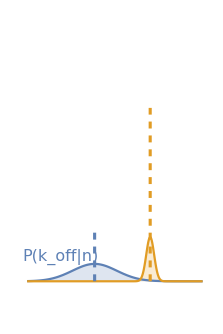
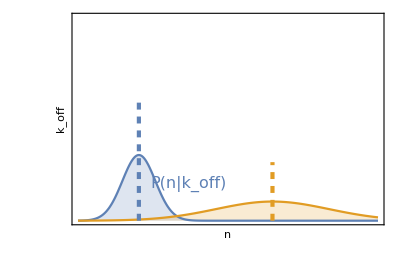

```mathematica
PnKofflabel=Style["P(n|k_off)",{FontSize->16,FontColor->cmap[[1]]}];
PKoffNlabel=Style["P(k_off|n)",{FontSize->16,FontColor->cmap[[1]]}];
MLElabel=Style["k_off^*=⟨n⟩^-1",16];
distParams={kon->1,kp->10,t->100,koff->10^gtest,δ->0.1,c->10^ctest,kf->1};

d1Params={ctest->0,gtest->1};
n1dist={μ1/.distParams/.d1Params//N,Σ1/.distParams/.d1Params//N};
κ1estimator/.{n->n1dist[[1]]}/.distParams/.d1Params;
Σk1/.{n->n1dist[[1]]}/.distParams/.{ctest->0,gtest->Log10[%]};
k1dist={%%,%};

d2Params={ctest->0,gtest->0.55};
n2dist={μ1/.distParams/.d2Params//N,Σ1/.distParams/.d2Params//N};
κ1estimator/.{n->n2dist[[1]]}/.distParams/.d2Params;
Σk1/.{n->n2dist[[1]]}/.distParams/.{ctest->1,gtest->Log10[%]};
k2dist={%%,%};

g1=
Show[
Plot[{PDF[NormalDistribution[n1dist[[1]],√n1dist[[2]]],x],PDF[NormalDistribution[n2dist[[1]],√n2dist[[2]]],x]},
{x,-10,80},
Frame->{{True,False},{True,False}},FrameLabel->{"n","k_off"},FrameStyle->{{{Black,Thickness[0.005]},None},{{Black,Thickness[0.005]},None}},LabelStyle->{Black,FontSize->16},FrameTicks->None,Axes->{False,False},PlotStyle->{cmap[[1]],cmap[[2]]},Filling->Axis,PlotRange->{{-10,80},{0,0.25}},AspectRatio->2/3,Epilog->Inset[PnKofflabel,{23,0.045}]],

ListPlot[Table[{n1dist[[1]],i},{i,0,0.15,0.01}],Axes->{False,False},Frame->False,Joined->True,PlotStyle->{cmap[[1]],Dashed,Thickness[0.0075]},PlotRange->{{-10,50},{0,0.25}},AspectRatio->2/3],

ListPlot[Table[{n2dist[[1]],i},{i,0,0.072,0.001}],Axes->{False,False},Frame->False,Joined->True,PlotStyle->{cmap[[2]],Dashed,Thickness[0.0075]},PlotRange->{{-10,50},{0,0.25}},AspectRatio->2/3]
];

g2=Plot[κ1estimator/.xgParams/.ctest->0,{n,2,80},
PlotRange->{{-20,80},{-2.7,6.5}},PlotStyle->{Black,Thickness[0.005]},Frame->False,Axes->False,AspectRatio->2/3,
Epilog->Inset[MLElabel,{60,1},Automatic,Automatic]];

g3=Rotate[
Show[

Plot[{PDF[NormalDistribution[k1dist[[1]],√k1dist[[2]]],-k],0.45*PDF[NormalDistribution[-1.78+k2dist[[1]],√k2dist[[2]]],-k]},
{k,-20,6},PlotStyle->{cmap[[1]],cmap[[2]]},
PlotRange->{{-21,6},{-0.155,1.75}},Filling->Axis,Frame->{{False,False},{False,False}},
FrameStyle->Black,LabelStyle->{Black,FontSize->16},FrameTicks->None,Axes->{False,False},AspectRatio->3/2,ImageSize->223,Epilog->Inset[PKoffNlabel,{-15,0.17}]],
ListPlot[Table[{-k1dist[[1]],i},{i,0,0.37,0.01}],Axes->{False,False},Frame->False,Joined->True,PlotStyle->{cmap[[1]],Dashed,Thickness[0.01]},PlotRange->{{-6.5,1},{-0.23,1.75}}],
ListPlot[Table[{1.78-k2dist[[1]],i},{i,0,1.21,0.01}],Axes->{False,False},Frame->False,Joined->True,PlotStyle->{cmap[[2]],Dashed,Thickness[0.01]},PlotRange->{{-6.5,1},{-0.23,1.75}}]

],-π/2];
Fig1C=Overlay[{g2,g3,g1}]
```

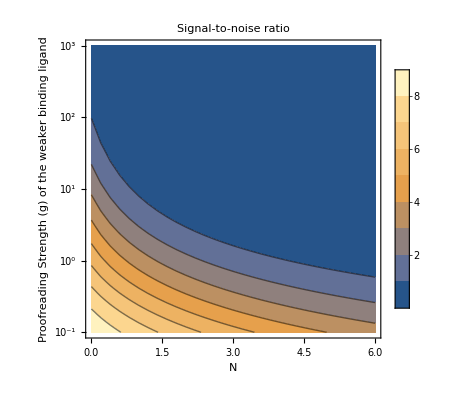

```mathematica
estimateParams={kon->1,kp->1,t->100,koff->10^gtest,c->10^ctest,kf->1};
plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)\n of  the weaker binding ligand"},
PlotLegends->Automatic,
PlotLabel->"Signal-to-noise ratio",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Automatic,None}}};
data=Flatten[Table[{NTEST,GTEST,μN/√ΣN}/.expandParams/.estimateParams/.{ctest->0,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.05},{NTEST,0,6,0.2}],1];
Fig2A=ListContourPlot[data,Evaluate@plotOptions]
```

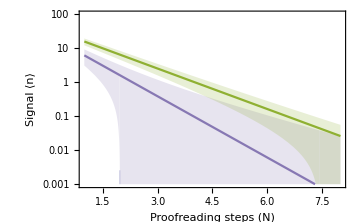

```mathematica
grep=g->3;
δrep={δ->0.5};
suppParams=Join[{kon->1,kp->1,t->100,koff->g,c->1,kf->1},δrep]/.grep;
curves1={μN,μN+√ΣN,Max[μN-√ΣN,10^-8]}/.expandParams/.suppParams;
curves2={μN,μN+√ΣN,Max[μN-√ΣN,10^-8]}/.{koff->δ koff}/.expandParams/.suppParams;
plotOptions={Filling->{1->{2},1->{3}},
LabelStyle->{Black,FontSize->18},
TicksStyle->Black,
ImageSize->Medium,
Frame->{{True,False},{True,False}},
Filling->{1->{2},1->{3},4->{5},6->{4}},
FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-9,4,1}],None},{Automatic,None}},
PlotRange->{{1,8},{10^-3,10^2}},
FrameLabel->{"Proofreading steps (N)","Signal ⟨n⟩"}};

g1=LogPlot[curves1,{Ns,1,8},PlotStyle->{cmap[[5]],None,None},Evaluate@plotOptions];
g2=LogPlot[curves2,{Ns,1,8},PlotStyle->{cmap[[3]],None,None},Evaluate@plotOptions];
Fig2B=Show[g1,g2]
```

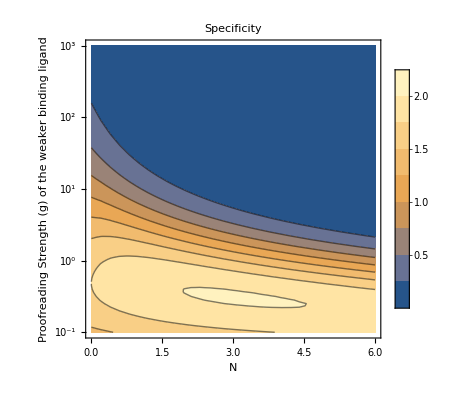

```mathematica
plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)\n of  the weaker binding ligand"},
PlotLegends->Automatic,
PlotLabel->"Specificity",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Automatic,None}}};
data=Flatten[Table[{NTEST,GTEST,koff/√ΣkN}/.xgParams/.{ctest->-1,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.05},{NTEST,0,6,0.2}],1];
EpilogPoint=MaximalBy[data,Last][[1]];
Fig2C=ListContourPlot[data,Evaluate@plotOptions]
```

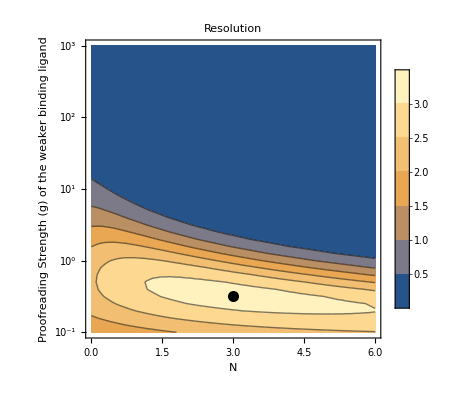

```mathematica
data=Flatten[Table[{NTEST,GTEST,BPMetric[koff,ΣkN]}/.xgParams/.{ctest->-1,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.1},{NTEST,0,6,0.2}],1];
EpilogPoint=MaximalBy[data,Last][[1]];
plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)\n of  the weaker binding ligand"},
PlotLegends->Automatic,
PlotLabel->"Resolution",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Automatic,None}}};
Fig3A=ListContourPlot[data,Evaluate@plotOptions,
Epilog->{PointSize[0.02],{Black,Point[{EpilogPoint[[1]],EpilogPoint[[2]]}]}}]
```

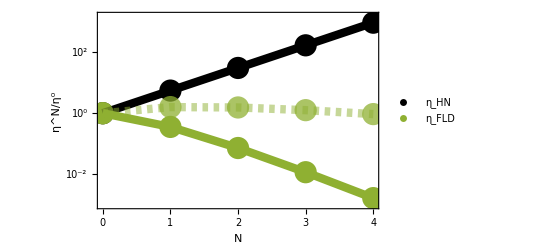

```mathematica
testpoint={ctest->0,gtest->1};
testpoint2={ctest->0,gtest->0};
yticks=Table[{2.301i,Superscript[10,i]},{i,-4,4}];
p1=ListLogPlot[Table[{Ns,ηN/η0}/.xgParams/.testpoint,{Ns,0,4,1}],Frame->{{True,False},{True,False}},FrameLabel->{"N","η^N/η^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{PointSize[0.04],Black},FrameTicks->{{yticks,None},{{0,1,2,3,4},None}},PlotRange->{Automatic,{0.001,1500}}];
p2=LogPlot[ηN/η0/.xgParams/.testpoint,{Ns,0,4},PlotStyle->{Thickness[0.015],Black}];



BPKscale={{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk}}/.expandParams/.xgParams/.testpoint;
BPKscale2={{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk}}/.expandParams/.xgParams/.testpoint2;
Fig3C=Legended[
Show[p1,p2,

ListLogPlot[BPKscale,PlotStyle->{cmap[[3]],PointSize[0.04]}],
ListLogPlot[BPKscale,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015]}],

ListLogPlot[BPKscale2,PlotStyle->{cmap[[3]],PointSize[0.04],Opacity[0.75]}],
ListLogPlot[BPKscale2,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015],Dashing[0.01],Opacity[0.5]}]
],
PointLegend[{Black,cmap[[3]]},{"η_HN","η_FLD"},LegendMarkerSize->25]]
```

```mathematica
{{0,1.00},{1,1920.92},{2,1438.04},{3,712.38},{4,282.37}}
```

### Export Figures

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
```

```mathematica
Export["Fig1B.pdf",Fig1B];
Export["Fig1C.pdf",Fig1C];
Export["Fig2A.pdf",Fig2A];
Export["Fig2B.pdf",Fig2B];
Export["Fig2C.pdf",Fig2C];
Export["Fig2D.pdf",Fig2D];
Export["Fig3A.pdf",Fig3A];
Export["Fig3B.pdf",Fig3B];
Export["Fig3C.pdf",Fig3C];
Export["FigS2.pdf",FigS2];
Export["FigS4.pdf",FigS4];
```

## Approximate Expressions

```mathematica
agonistKOFFstrong=1/10;
agonistKOFFweak=1/1;
nonagonistKOFFstrong=1/3;
nonagonistKOFFweak=1/0.3;
kfPettman=1/2.8;

gForWeakLigand={nonagonistKOFFstrong/kfPettman,nonagonistKOFFweak/kfPettman}
gForStrongLigand={agonistKOFFstrong/kfPettman,agonistKOFFweak/kfPettman}
```

{0.933333,9.33333}

{0.28,2.8}

```mathematica
agonistKOFFstrong/kfPettman
```

0.28

```mathematica
nonagonistKOFFweak
nonagonistKOFFstrong//N
```

3.33333

0.333333

## Mean Expressions

```mathematica
μ1==n/.expandParams
koff/.Solve[%,koff][[1]]
Assuming[n>0&&koff>0&&g>0&&Element[n,Reals],Simplify[%]]
```

(c kon kp t)/(koff (1+koff/kf) (1+(c kon)/koff))==n

(-kf n-c kon n+√n √(kf^2 n-2 c kf kon n+c^2 kon^2 n+4 c kf kon kp t))/(2 n)

1/2 (-kf-c kon+√(kf^2-2 c kf kon+c^2 kon^2+(4 c kf kon kp t)/n))

```mathematica
kf/2 (-1-(c kon)/kf+√(1+((kon c)/kf)^2+(c kon)/kf((4  kp t)/n-2)))
```

1/2 kf (-1-(c kon)/kf+√(1+(c^2 kon^2)/kf^2+(c kon (-2+(4 kp t)/n))/kf))

```mathematica
Σk1/.{c->kf/kon y,koff->kf g}//FullSimplify
```

1/(kp t y (1+2 g+y)^2)(1+g) kf (g+y) (g (1+g)^2 (g kf+2 kp)+2 g ((1+g)^2 kf+kp+2 g kp) y+((1+g)^2 kf+2 g kp) y^2)

```mathematica
((1+g) kf (g+y))/(kp t y (1+2 g+y)^2) ( y^2 q+2 y g (q+kp)+g^2( q+(2 kp)/g+4 kp ))/.{q->(1+g)^2 kf+2 g kp};

%-(1/(kp t y (1+2 g+y)^2)(1+g) kf (g+y) (g (1+g)^2 (g kf+2 kp)+2 g ((1+g)^2 kf+kp+2 g kp) y+((1+g)^2 kf+2 g kp) y^2))//Simplify
```

0

```mathematica
((1+g) kf (g+y))/(kp t y (1+2 g+y)^2) ( y^2 q+2 y g (q+kp)+g^2( q+(2 kp)/g+4 kp ))//FullSimplify
```

((1+g) kf (g+y) (g^2 (4 kp+q)+q y^2+2 g (kp+(kp+q) y)))/(kp t y (1+2 g+y)^2)

## Specificity

```mathematica
ηFLDN=BPMetric[koff,ΣkN]/.contractParams//FullSimplify
```

(koff kp t x (-1+δ)^2)/(((1+g)^(2+Ns) (koff+2 kp) (1+x)^3-2 (1+g) kp x (1+x) (2+x+g (2+Ns+x+Ns x)))/(1+g (1+Ns+Ns x))^2+((x+δ) (1+g δ) ((x+δ)^2 (1+g δ)^(1+Ns) (2 kp+koff δ)-2 kp x (x+g (1+Ns) x δ+δ (2+g (2+Ns) δ))))/(δ (1+g (δ+Ns (x+δ)))^2))

```mathematica
Limit[ηFLDN,g->0]//Simplify
```

(koff kp t x (-1+δ)^2)/(2 kp (1+x+x δ+δ^2)+koff (1+2 x^3+δ^3+3 x^2 (1+δ)+3 x (1+δ^2)))

```mathematica
ηFLDN/.Ns->0//Simplify
```

(koff kp t x (-1+δ)^2)/(2 kp (1+x+x δ+δ^2)+koff (1+2 x^3+δ^3+3 x^2 (1+δ)+3 x (1+δ^2)))

```mathematica
Assuming[δ>0&&δ<1&&δ∈Reals&&g>0&&x>0,Limit[(1+g)^(2+Ns)/(1+g (1+Ns+Ns x))^2,Ns->Infinity]]
Assuming[δ>0&&δ<1&&δ∈Reals&&g>0&&x>0,Limit[(-2 (1+g) kp x (1+x) (2+x+g (2+Ns+x+Ns x)))/(1+g (1+Ns+Ns x))^2,Ns->Infinity]]
Assuming[δ>0&&δ<1&&δ∈Reals&&g>0&&x>0,Limit[((x+δ) (1+g δ) ((x+δ)^2 (1+g δ)^(1+Ns) (2 kp+koff δ)))/(δ (1+g (δ+Ns (x+δ)))^2),Ns->Infinity]]
Assuming[δ>0&&δ<1&&δ∈Reals&&g>0&&x>0,Limit[((x+δ) (1+g δ) (-2 kp x (x+g (1+Ns) x δ+δ (2+g (2+Ns) δ))))/(δ (1+g (δ+Ns (x+δ)))^2),Ns->Infinity]]
```

∞

0

(2 kp+koff δ) ∞

0

So we can neglect the second term in each component of the denominator in the limit of large N, to get a simplified expression:

```mathematica
FullSimplify[(koff kp t x (-1+δ)^2)/(((1+g)^(2+Ns) (koff+2 kp) (1+x)^3)/(1+g (1+Ns+Ns x))^2+((x+δ) (1+g δ) ((x+δ)^2 (1+g δ)^(1+Ns) (2 kp+koff δ)))/(δ (1+g (δ+Ns (x+δ)))^2))]
```

(koff kp t x (-1+δ)^2)/(((1+g)^(2+Ns) (koff+2 kp) (1+x)^3)/(1+g (1+Ns+Ns x))^2+((x+δ)^3 (1+g δ)^(2+Ns) (2 kp+koff δ))/(δ (1+g (δ+Ns (x+δ)))^2))

```mathematica
ηFLDHighN=(kp t x (δ-1)^2)/(((1+g)^(2+Ns) (1+2 kp/koff) (1+x)^3)/(1+g (1+Ns+Ns x))^2+((1+g δ)^(2+Ns) (1+2/δ kp/koff)(δ+x)^3)/(1+g (δ+Ns δ+Ns x))^2);
```

```mathematica
(kp t x (δ-1)^2(1+g (1+Ns+Ns x))^2)/((1+g)^(2+Ns) (1+2 kp/koff) (1+x)^3+((1+g (1+Ns+Ns x))/(1+g (δ+Ns δ+Ns x)))^2(1+g δ)^(2+Ns) (1+2/δ kp/koff)(δ+x)^3)-ηFLDHighN//Simplify
```

0

```mathematica
Limit[((1+g (1+Ns+Ns x))/(1+g (δ+Ns δ+Ns x)))^2,Ns->Infinity]
```

(1+x)^2/(x+δ)^2

```mathematica
ηFLDHighN=(kp t x (δ-1)^2(1+g (1+Ns+Ns x))^2)/((1+g)^(2+Ns) (1+2 kp/koff) (1+x)^3+((1+x)/(δ+x))^2(1+g δ)^(2+Ns) (1+2/δ kp/koff)(δ+x)^3);
```

```mathematica
(kp t x (δ-1)^2(1+g (1+Ns+Ns x))^2)/(1+g)^(2+Ns)1/((1+2 kp/koff) (1+x)^3+((1+x)/(δ+x))^2(1+g δ)^(2+Ns)/(1+g)^(2+Ns) (1+2/δ kp/koff)(δ+x)^3)-ηFLDHighN//Simplify
```

0

So for small δ this term is basically 0 while for δ≈1 this term is basically 1.
However, even for δ≈1 the term becomes zero for sufficiently large N:

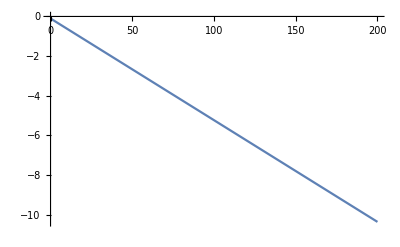

```mathematica
Plot[Log@(((1+g δ)/(1+g))^(2+Ns))/.{g->1,δ->0.9},{Ns,0,200}]
```

```mathematica
smallerHighNFLD=(kp t x (1-δ)^2)/((1+x)^3(1+2 kp/koff))(1+g+Ns g(1+x))^2/(1+g)^(2+Ns);
questionableHighNFLD=((1-δ)^2(1+g+Ns g(1+x))^2)/(1+g)^(2+Ns);
```

```mathematica
Assuming[g>0&&x>0,Limit[questionableHighNFLD,Ns->Infinity]]
```

0

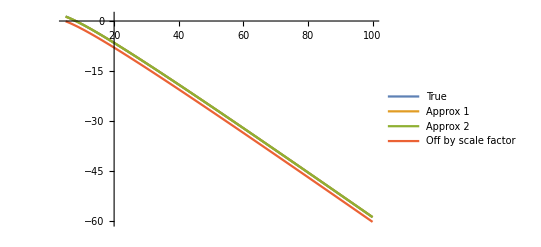

```mathematica
testParams={kp->1,t->100,x->1,koff->1,g->1,δ->0.1};
Plot[{
Log@ηFLDN/.testParams,
Log@ηFLDHighN/.testParams,
Log@smallerHighNFLD/.testParams,
Log@questionableHighNFLD/.testParams},
{Ns,5,100},PlotLegends->{"True","Approx 1","Approx 2","Off by scale factor"},PlotRange->All]
```

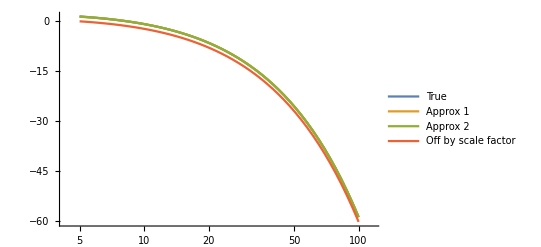

```mathematica
testParams={kp->1,t->100,x->1,koff->1,g->1,δ->0.1};
LogLinearPlot[{
Log@ηFLDN/.testParams,
Log@ηFLDHighN/.testParams,
Log@smallerHighNFLD/.testParams,
Log@questionableHighNFLD/.testParams},
{Ns,5,100},PlotLegends->{"True","Approx 1","Approx 2","Off by scale factor"},PlotRange->All]
```

#### Scaling relative to N=0

```mathematica
ηFLD0=BPMetric[koff,Σk0]/.contractParams//FullSimplify
```

(koff kp t x (-1+δ)^2)/(koff (1+2 x+δ) (1+x+x^2+(-1+x) δ+δ^2)+2 kp (1+x+x δ+δ^2))

```mathematica
smallerHighNFLD/ηFLD0//FullSimplify
```

1/((koff+2 kp) (1+x)^3)(1+g)^(-2-Ns) (1+g (1+Ns+Ns x))^2 (koff (1+2 x+δ) (1+x+x^2+(-1+x) δ+δ^2)+2 kp (1+x+x δ+δ^2))

```mathematica
Assuming[δ>0&&δ<1&&δ∈Reals&&g>0&&x>0,Limit[1/((koff+2 kp) (1+x)^3)(1+g)^(-2-Ns) (1+g (1+Ns+Ns x))^2 (koff (1+2 x+δ) (1+x+x^2+(-1+x) δ+δ^2)+2 kp (1+x+x δ+δ^2)),Ns->Infinity]]
```

0

```mathematica
((1+g (1+Ns+Ns x))^2 ((1+2 x+δ) ((1+x)^2+(δ+x)(δ-1))+2 kp/koff ((δ+x)(δ+1)-(δ-1))))/((1+2 kp/koff) (1+x)^3(1+g)^(2+Ns))
```

```mathematica
Collect[(2 kp (1+x+x δ+δ^2))/koff+(1+2 x+δ) ((1+x)^2+(-1+δ) (x+δ)),δ]
```

(2 kp)/koff-x+(2 kp x)/koff-2 x^2+(1+x)^2+2 x (1+x)^2+(-1-2 x+(2 kp x)/koff+2 x^2+(1+x)^2) δ+((2 kp)/koff+3 x) δ^2+δ^3

```mathematica
(*BigOscaling=(1+g (1+Ns+Ns x))^2/((1+2 kp/koff) (1+x)^3(1+g)^(2+Ns))δ^3;*)
ManuscriptScaling=((Ns x g)^2 δ^3)/(1+g)^(2+Ns);
```

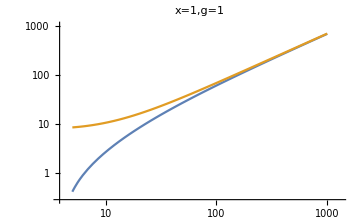
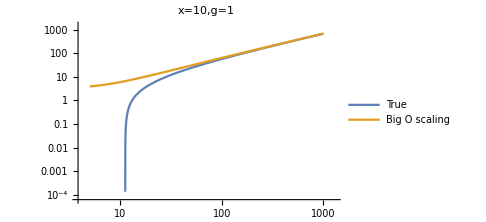

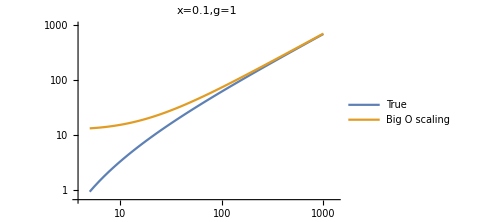
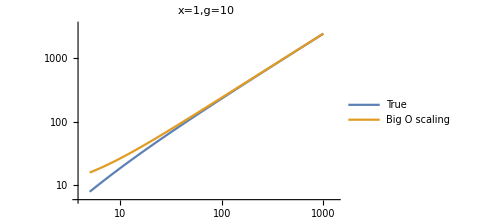

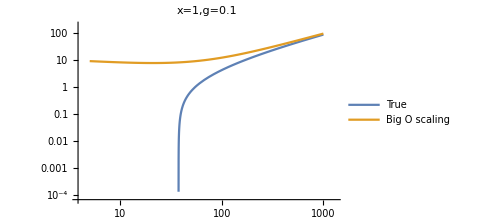
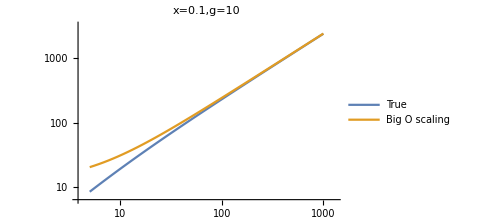

```mathematica
testParams={kp->1,t->100,x->1,koff->1,g->1,δ->0.1};
g1=LogLogPlot[{
-Log@(KPRNBPk/KPR0BPk)/.contractParams/.testParams,
(*-Log@BigOscaling/.testParams,*)
-Log@ManuscriptScaling/.{ζ->δ}/.testParams},
{Ns,5,1000},PlotRange->All,ImageSize->Medium,PlotLabel->"x=1,g=1"];

testParams={kp->1,t->100,x->10,koff->1,g->1,δ->0.1};
g2=LogLogPlot[{
-Log@(KPRNBPk/KPR0BPk)/.contractParams/.testParams,
(*-Log@BigOscaling/.testParams,*)
-Log@ManuscriptScaling/.{ζ->δ}/.testParams},
{Ns,5,1000},PlotLegends->{"True","Big O scaling"},PlotRange->All,ImageSize->Medium,PlotLabel->"x=10,g=1"];

testParams={kp->1,t->100,x->0.1,koff->1,g->1,δ->0.1};
g3=LogLogPlot[{
-Log@(KPRNBPk/KPR0BPk)/.contractParams/.testParams,
(*-Log@BigOscaling/.testParams,*)
-Log@ManuscriptScaling/.{ζ->δ}/.testParams},
{Ns,5,1000},PlotLegends->{"True","Big O scaling"},PlotRange->All,ImageSize->Medium,PlotLabel->"x=0.1,g=1"];

testParams={kp->1,t->100,x->1,koff->1,g->10,δ->0.1};
g4=LogLogPlot[{
-Log@(KPRNBPk/KPR0BPk)/.contractParams/.testParams,
(*-Log@BigOscaling/.testParams,*)
-Log@ManuscriptScaling/.{ζ->δ}/.testParams},
{Ns,5,1000},PlotLegends->{"True","Big O scaling"},PlotRange->All,ImageSize->Medium,PlotLabel->"x=1,g=10"];


testParams={kp->1,t->100,x->1,koff->1,g->0.1,δ->0.1};
g5=LogLogPlot[{
-Log@(KPRNBPk/KPR0BPk)/.contractParams/.testParams,
(*-Log@BigOscaling/.testParams,*)
-Log@ManuscriptScaling/.{ζ->δ}/.testParams},
{Ns,5,1000},PlotLegends->{"True","Big O scaling"},PlotRange->All,ImageSize->Medium,PlotLabel->"x=1,g=0.1"];


testParams={kp->1,t->100,x->0.1,koff->1,g->10,δ->0.1};
g6=LogLogPlot[{
-Log@(KPRNBPk/KPR0BPk)/.contractParams/.testParams,
(*-Log@BigOscaling/.testParams,*)
-Log@ManuscriptScaling/.{ζ->δ}/.testParams},
{Ns,5,1000},PlotLegends->{"True","Big O scaling"},PlotRange->All,ImageSize->Medium,PlotLabel->"x=0.1,g=10"];
Row[{g1,g2}]
Row[{g3,g4}]
Row[{g5,g6}]
```

```mathematica
Assuming[δ>0&&δ<1&&δ∈Reals&&g>0&&x>0,Limit[ManuscriptScaling,Ns->Infinity]]
```

0

#### Alternate derivation of optimal N

Choose the axes determined by numerically evaluating location of (y_max,g_max) for different N and finding minimal y_max and g_max. Make these the most probable y and g respectively, and assign unit-variance lognormal prior probabilities of encountering y and g centered on these values. Find the PDF-weighted maximal η_FLD with these priors. The optimal number of proofreading steps is N=2.8

```mathematica
ηFLDNExpanded=Evaluate[Evaluate[ηFLDN/.{x->y/g}]/.g->koff/kf]/.{koff->10^KOFFTEST,y->10^YTEST};
ηFLDPosterior=ηFLDNExpanded(PDF[NormalDistribution[Log[3],1],YTEST]PDF[NormalDistribution[Log[0.5],1],KOFFTEST])/.{kp->1,t->100,kf->1,δ->0.1};
NMaximize[ηFLDPosterior,{Ns,KOFFTEST,YTEST}]
```

{1.29877,{Ns→2.80579,KOFFTEST→-0.16528,YTEST→1.06092}}

```mathematica
10^-0.1652804475236378
```

0.68347

#### Enhancement

```mathematica
ηFLDNo0=BPMetric[koff,ΣkN]/BPMetric[koff,Σk0]//Simplify;
```

```mathematica
ηFLDNo0Contract=ηFLDNo0/.{c->y kf/kon,koff->g kf}//Simplify;
Limit[ηFLDNo0Contract,g->0]
Limit[ηFLDNo0Contract,y->0]//Simplify
```

(1+Ns y)^2

((1+g+g Ns)^2 (1+g (1+Ns) δ)^2 (2 kp (1+δ^2)+g kf (1+δ^3)))/(2 kp ((1+g)^Ns+δ^2 (1+g δ)^Ns)+g^5 kf (1+Ns)^2 δ^2 ((1+g)^Ns+δ^3 (1+g δ)^Ns)+g (kf ((1+g)^Ns+δ^3 (1+g δ)^Ns)+4 kp ((1+g)^Ns+(1+g)^Ns (1+Ns) δ+(1+Ns) δ^2 (1+g δ)^Ns+δ^3 (1+g δ)^Ns))+2 g^4 (1+Ns) δ (kp (1+Ns) δ ((1+g)^Ns+δ^2 (1+g δ)^Ns)+kf ((1+g)^Ns+(1+g)^Ns (1+Ns) δ+(1+Ns) δ^3 (1+g δ)^Ns+δ^4 (1+g δ)^Ns))+g^3 (4 kp (1+Ns) δ ((1+g)^Ns+(1+g)^Ns (1+Ns) δ+(1+Ns) δ^2 (1+g δ)^Ns+δ^3 (1+g δ)^Ns)+kf ((1+g)^Ns+4 (1+g)^Ns (1+Ns) δ+(1+g)^Ns (1+Ns)^2 δ^2+(1+Ns)^2 δ^3 (1+g δ)^Ns+4 (1+Ns) δ^4 (1+g δ)^Ns+δ^5 (1+g δ)^Ns))+2 g^2 (kf ((1+g)^Ns+(1+g)^Ns (1+Ns) δ+(1+Ns) δ^3 (1+g δ)^Ns+δ^4 (1+g δ)^Ns)+kp ((1+g)^Ns+4 (1+g)^Ns (1+Ns) δ+4 (1+Ns) δ^3 (1+g δ)^Ns+δ^4 (1+g δ)^Ns+(1+Ns)^2 δ^2 ((1+g)^Ns+(1+g δ)^Ns))))

So in the limit of low concentration this is approximately 1 (no enhancement) and in the limit of large concentration this is O{(N y)^2}

#### FLD resolution as N→∞ and g→0 along contours of constant Hopfield resolution

```mathematica
ηN/η0/.contractParams/.δ->ζ
Solve[((1+g)/(1+g ζ))^Ns==C1,g][[1]]
(KPRNBPk/KPR0BPk/.contractParams/.δ->ζ//Simplify)/.{g->(1-C1^(1/Ns))/(-1+C1^(1/Ns) ζ)}//Simplify;
Limit[%,Ns->∞]//FullSimplify
Series[%,{x,0,0}]
```

(koff+koff/g)^Ns (koff/g+koff ζ)^-Ns

{g→(1-C1^(1/Ns))/(-1+C1^(1/Ns) ζ)}

(koff (1+2 x+ζ) (1+x+x^2+(-1+x) ζ+ζ^2)+2 kp (1+x+x ζ+ζ^2))/((-1+ζ) ((C1^(1/(1-ζ)) (1+x) ((koff+2 kp) (1+x)^2 (-1+ζ)-2 C1^(1/(-1+ζ)) kp x ((2+x) (-1+ζ)-(1+x) Log[C1])))/(1-ζ+(1+x) Log[C1])^2+(C1^(-ζ/(-1+ζ)) ((-1+ζ) (x+ζ)^3 (2 kp+koff ζ)+2 C1^(ζ/(-1+ζ)) kp x (x+ζ) (-(-1+ζ) (x+2 ζ)+ζ (x+ζ) Log[C1])))/(ζ (1-ζ+(x+ζ) Log[C1])^2)))

(koff+2 kp+2 kp ζ^2+koff ζ^3)/((-1+ζ) ((C1^(1/(1-ζ)) (koff+2 kp) (-1+ζ))/(1-ζ+Log[C1])^2+(C1^(-ζ/(-1+ζ)) (-1+ζ) ζ^2 (2 kp+koff ζ))/(1-ζ+ζ Log[C1])^2))+O[x]^1

```mathematica
Numerator[D[(1+2+2 ζ^2+ζ^3)/((-1+ζ) ((C1^(1/(1-ζ)) (1+2 kp) (-1+ζ))/(1-ζ+Log[C1])^2+(C1^(-ζ/(-1+ζ)) (-1+ζ) ζ^2 (2 + ζ))/(1-ζ+ζ Log[C1])^2)),C1]]//Simplify
Solve[%==0,C1]
```

((3+2 ζ^2+ζ^3) (-(2 C1^(1/(1-ζ)) (1+2 kp) (-1+ζ))/(-1+ζ-Log[C1])^3+(C1^(1/(1-ζ)) (1+2 kp))/(1-ζ+Log[C1])^2+(2 C1^(-ζ/(-1+ζ)) (-1+ζ) ζ^3 (2+ζ))/(1-ζ+ζ Log[C1])^3+(C1^(-ζ/(-1+ζ)) ζ^3 (2+ζ))/(1-ζ+ζ Log[C1])^2))/C1

Solve[((3+2 ζ^2+ζ^3) (-(2 C1^(1/(1-ζ)) (1+2 kp) (-1+ζ))/(-1+ζ-Log[C1])^3+(C1^(1/(1-ζ)) (1+2 kp))/(1-ζ+Log[C1])^2+(2 C1^(-ζ/(-1+ζ)) (-1+ζ) ζ^3 (2+ζ))/(1-ζ+ζ Log[C1])^3+(C1^(-ζ/(-1+ζ)) ζ^3 (2+ζ))/(1-ζ+ζ Log[C1])^2))/C1==0,C1]

```mathematica
ηFLDatN∞=(koff (1+2 x+ζ) (1+x+x^2+(-1+x) ζ+ζ^2)+2 kp (1+x+x ζ+ζ^2))/((-1+ζ) ((C1^(1/(1-ζ)) (1+x) ((koff+2 kp) (1+x)^2 (-1+ζ)-2 C1^(1/(-1+ζ)) kp x ((2+x) (-1+ζ)-(1+x) Log[C1])))/(1-ζ+(1+x) Log[C1])^2+(C1^(-ζ/(-1+ζ)) ((-1+ζ) (x+ζ)^3 (2 kp+koff ζ)+2 C1^(ζ/(-1+ζ)) kp x (x+ζ) (-(-1+ζ) (x+2 ζ)+ζ (x+ζ) Log[C1])))/(ζ (1-ζ+(x+ζ) Log[C1])^2)));
```

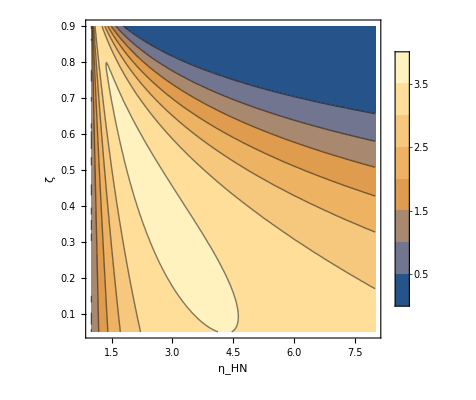

```mathematica
ContourPlot[ηFLDatN∞/.{koff->1,kp->0.1,x->1},{C1,1,8},{ζ,0.05,0.9},PlotLegends->Automatic,FrameLabel->{"η_HN","ζ"},LabelStyle->{Black,FontSize->16}]
```

```mathematica
(koff+2 kp+2 kp ζ^2+koff ζ^3)/((-1+ζ) ((C1^(1/(1-ζ)) (koff+2 kp) (-1+ζ))/(1-ζ+Log[C1])^2+(C1^(-ζ/(-1+ζ)) (-1+ζ) ζ^2 (2 kp+koff ζ))/(1-ζ+ζ Log[C1])^2))
```

(Ns^2 ζ ((1+C1^(3/Ns)) koff (-1+ζ)^2+2 (-1+C1^(1/Ns))^2 kp (C1^(1/Ns)+ζ)))/((-1+C1^(1/Ns) ζ) (koff (-1+ζ) ζ (((-1+ζ)/(-1+C1^(1/Ns) ζ))^Ns+C1^(2/Ns) ((C1^(1/Ns) (-1+ζ))/(-1+C1^(1/Ns) ζ))^Ns)+2 kp (1-((-1+ζ)/(-1+C1^(1/Ns) ζ))^Ns+C1^(2/Ns) ζ^2 (-1+((C1^(1/Ns) (-1+ζ))/(-1+C1^(1/Ns) ζ))^Ns)+ζ (-1-Ns+((-1+ζ)/(-1+C1^(1/Ns) ζ))^Ns+C1^(2/Ns) (1+Ns-((C1^(1/Ns) (-1+ζ))/(-1+C1^(1/Ns) ζ))^Ns)))))

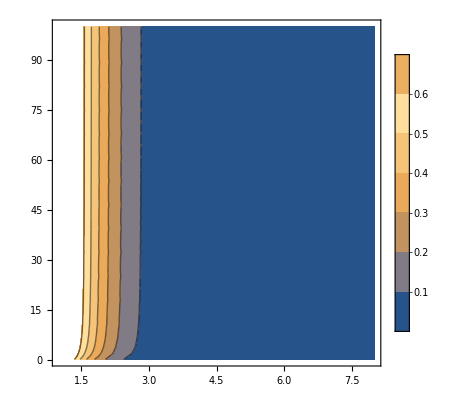

```mathematica
ηFLDN1xHigh=Limit[Evaluate[KPRNBPk/KPR1BPk/.contractParams/.δ->ζ],x->Infinity]//Simplify;
ηFLDN1xHighgR1=%/.{g->(1-C1^(1/Ns))/(-1+C1^(1/Ns) ζ)}//Simplify
ContourPlot[KPRNBPk/KPR1BPk/.contractParams/.δ->ζ/.{koff->1,kp->1,ζ->0.5,g->10,t->100},{Ns,1,8},{x,0.1,100},PlotLegends->Automatic]
```

```mathematica
D[KPRNBPk,Ns]/.contractParams/.δ->ζ/.{koff->1,kp->1,ζ->0.5,g->10,t->100,Ns->1,x->2}
```

-0.710348

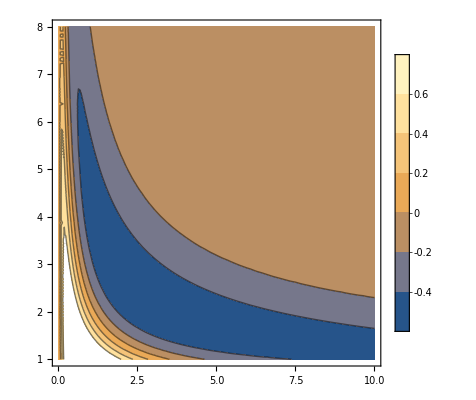

```mathematica
ContourPlot[Evaluate[D[KPRNBPk,Ns]/.contractParams/.δ->ζ/.{koff->1,kp->1,ζ->0.5,x->10,t->100}],{g,0.01,10},{Ns,1,8},PlotLegends->Automatic]
```

```mathematica
-((Sign[(-1/(1+g (1+Ns+Ns x))^3 2 g (1+g) (1+x)^2 ((1+g)^(1+Ns) koff (1+x)^2+2 kp ((1+g)^Ns+2 (-1+(1+g)^Ns) x+(-1+(1+g)^Ns) x^2+g ((1+g)^Ns+(-2+2 (1+g)^Ns-Ns) x+(-1+(1+g)^Ns-Ns) x^2)))-1/(δ (1+g (δ+Ns (x+δ)))^3)2 g (x+δ)^2 (1+g δ) (koff δ (x+δ)^2 (1+g δ)^(1+Ns)+2 kp (δ^2 (1+g δ)^(1+Ns)+x^2 (-1+(1+g δ)^Ns+g δ (-1-Ns+(1+g δ)^Ns))+x δ (2 (-1+(1+g δ)^Ns)+g δ (-2-Ns+2 (1+g δ)^Ns))))+((1+g) (1+x)^2 (-2 g kp x+(1+g)^(1+Ns) (koff+2 kp) (1+x) Log[1+g]))/(1+g (1+Ns+Ns x))^2+((x+δ)^2 (1+g δ) (-2 g kp x δ+(x+δ) (1+g δ)^(1+Ns) (2 kp+koff δ) Log[1+g δ]))/(δ (1+g (δ+Ns (x+δ)))^2))]))
```

## Supplementary Figures

```mathematica
(*
 From: https://mathematica.stackexchange.com/questions/174124/extract-colorrange-of-contourplot *)
Clear[legendExtract];
Options[legendExtract]={"RGBasReal"->False};
legendExtract[plot_Legended,OptionsPattern[]]:=Module[{legend=plot[[2,1]],colordata,range,out},(*Extract colorfunction used in plot and the range of values used in the color scaling*){colordata,range}=legend[[1]]/.{b_Blend&:>b[[1]]};
(*Create list of values and colors used in legend*)out={#,ColorData[colordata][Rescale[#,range]]}&/@legend[[2]]/.{{y_Real,_}:>y};
(*If desired,output RGB values as real numbers instead of swatches*)If[OptionValue["RGBasReal"]==True,out/.{RGBColor[vals__]:>vals},out]];

testPlot=ContourPlot[Log10[KPR1BPk/KPR0BPk]/.xgParams,{ctest,-3,3},{gtest,-1,3},PlotLegends->Automatic];
contourcmap=Table[legendExtract[testPlot][[i,2]],{i,1,Length[legendExtract[testPlot]]}];
```

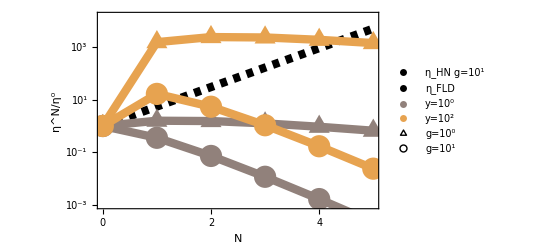

```mathematica
testpoint={ctest->0,gtest->1};
ExpandedYTicks=Table[{2.301i,Superscript[10,i]},{i,-3,4}];
l1=ListLogPlot[Table[{Ns,ηN/η0}/.xgParams/.testpoint,{Ns,0,5,1}],Frame->{{True,False},{True,False}},FrameLabel->{"N","η^N/η^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{White,PointSize[0.04]},FrameTicks->{{ExpandedYTicks,None},{{0,1,2,3,4,5},None}},PlotRange->{Automatic,{0.001,15000}}];
l2=LogPlot[ηN/η0/.xgParams/.testpoint,{Ns,0,5},PlotStyle->{Black,Dashed,Thickness[0.015]}];

testpoint={ctest->0,gtest->0};
l3=ListLogPlot[{{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk},{5,KPR5BPk/KPR0BPk/.expandParams}}/.xgParams/.testpoint,PlotMarkers->{▲,25},PlotStyle->{contourcmap[[3]]}];
l4=ListLogPlot[{{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk},{5,KPR5BPk/KPR0BPk/.expandParams}}/.xgParams/.testpoint,Joined->True,PlotStyle->{contourcmap[[3]],Thickness[0.015]}];

testpoint={ctest->0,gtest->1};
l5=ListLogPlot[{{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk},{5,KPR5BPk/KPR0BPk/.expandParams}}/.xgParams/.testpoint,PlotStyle->{contourcmap[[3]],PointSize[0.04]}];
l6=ListLogPlot[{{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk},{5,KPR5BPk/KPR0BPk/.expandParams}}/.xgParams/.testpoint,Joined->True,PlotStyle->{contourcmap[[3]],Thickness[0.015]}];

testpoint={ctest->2,gtest->1};
l7=ListLogPlot[{{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk},{5,KPR5BPk/KPR0BPk/.expandParams}}/.xgParams/.testpoint,PlotStyle->{contourcmap[[5]],PointSize[0.04]}];
l8=ListLogPlot[{{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk},{5,KPR5BPk/KPR0BPk/.expandParams}}/.xgParams/.testpoint,Joined->True,PlotStyle->{contourcmap[[5]],Thickness[0.015]}];

testpoint={ctest->2,gtest->0};
l9=ListLogPlot[{{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk},{5,KPR5BPk/KPR0BPk/.expandParams}}/.xgParams/.testpoint,PlotMarkers->{▲,25},PlotStyle->{contourcmap[[5]],PointSize[0.04]}];
l10=ListLogPlot[{{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk},{5,KPR5BPk/KPR0BPk/.expandParams}}/.xgParams/.testpoint,Joined->True,PlotStyle->{contourcmap[[5]],Thickness[0.015]}];

Legended[
Show[l1,l2,l3,l4,l5,l6,l9,l10,l7,l8],
PointLegend[{Black,None,contourcmap[[3]],contourcmap[[5]],None,None,Black,Black},{"η_HN   g=10^1","                   η_FLD","y=10^0","y=10^2","","","g=10^0","g=10^1"},LegendMarkerSize->25,LegendLayout->{"Column",2},LegendMarkers->{{"■■",12},{"",0},{"●",18},{"●",18},{"",18},{"",18},{"△",25},{"○",20}}]]
```

```mathematica
FLDkN=BPMetric[koff,ΣkN];
pointEq=FLDkN/KPR0BPk/.xgParams;
pointEqFunc[CTEST_,GTEST_]:=Module[{expression=pointEq/.{ctest->CTEST,gtest->GTEST}},Ns/.NMaximize[{expression,Ns≥0},Ns][[2]]]
```

```mathematica
FigS1=ContourPlot[pointEqFunc[c1,g1],{c1,-3,3},{g1,-1,3},FrameLabel->{"Ligand concentration  (y)","Proofreading strength  (g)"},PlotLegends->Automatic,PlotLabel->"N^opt",LabelStyle->{Black,FontSize->18},TicksStyle->Black,FrameTicks->xgTicks,PlotRange->All,Contours->{0,1,2,3,4,5,6,7,8,9,10}]
```

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["FigS1.pdf",FigS1];
```

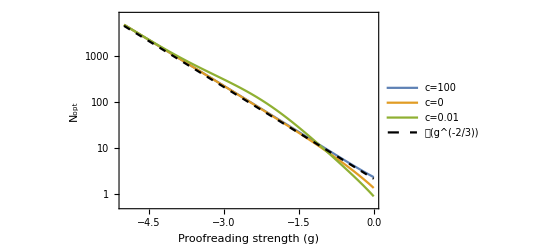

```mathematica
LogPlot[{pointEqFunc[2,g1],pointEqFunc[0,g1],pointEqFunc[-2,g1],10^(1/3-(2g1)/3)},{g1,-5,0},Frame->True,FrameLabel->{"Proofreading strength  (g)","N_opt"},LabelStyle->{Black,FontSize->18},TicksStyle->Black,PlotRange->All,PlotLegends->{"c=100","c=0","c=0.01","𝒪(g^(-2/3))"},PlotStyle->{Automatic,Automatic,Automatic,{Black,Dashed}}]
```

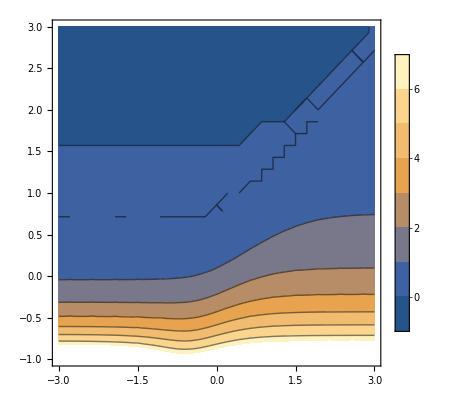

```mathematica
estimateParams={kon->1,kp->1,t->100,koff->10^gtest,δ->0.1,c->10^ctest,kf->1};
ContourPlot[Ns/.NMaximize[{koff/√ΣkN/.estimateParams/.{ctest->CTEST,gtest->GTEST},Ns∈Reals&&Ns≥0},Ns][[2]],{CTEST,-3,3},{GTEST,-1,3},PlotLegends->Automatic]
```

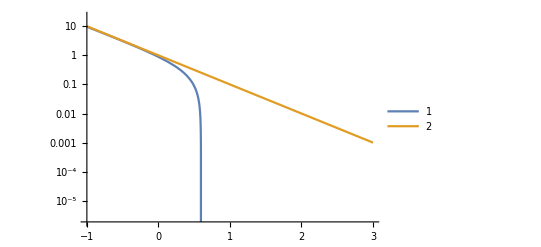

```mathematica
LogPlot[{Ns/.NMaximize[{koff/√ΣkN/.estimateParams/.{ctest->-2,gtest->GTEST},Ns∈Reals&&Ns≥0},Ns][[2]],10^-GTEST},{GTEST,-1,3},PlotLegends->Automatic]
```

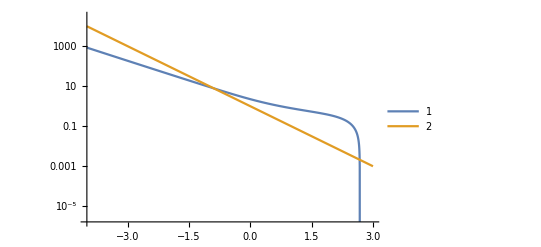

```mathematica
LogPlot[{Ns/.NMaximize[{koff/√ΣkN/.estimateParams/.{ctest->3,gtest->GTEST},Ns∈Reals&&Ns≥0},Ns][[2]],10^-GTEST},{GTEST,-4,3},PlotLegends->Automatic]
```

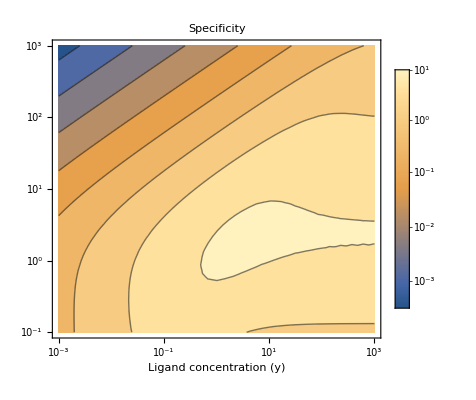

```mathematica
FigS1DtickSFs={1.068,1.065,1.04,1.5,1};
FigS1Dticks={#[[1]],Style[#[[2]],{Black,FontSize->18}]}&/@Table[{i,Superscript[10,i]},{i,-3,1,1}];
FigS1Dticks=Table[{FigS1DtickSFs[[i]]*FigS1Dticks[[i,1]],FigS1Dticks[[i,2]]},{i,1,Length[FigS1Dticks]}];
FigS1DbarLegend=Overlay[{BarLegend[{"M10DefaultDensityGradient",{-3.75,1}},LegendMarkerSize->250,LegendMargins->{{0,0},{20,0}},Ticks->FigS1Dticks,LabelStyle->Black],
BarLegend[{"M10DefaultDensityGradient",{-3.75,1}},8,LegendMarkerSize->250,LegendMargins->{{0,0},{20,0}},Ticks->None]}];

FigS1D=ContourPlot[Log10[SnRBP]/.expandParams/.xgParams,{ctest,-3,3},{gtest,-1,3},FrameLabel->{"Ligand concentration  (y)",None},PlotLegends->FigS1DbarLegend,PlotLabel->"Specificity",LabelStyle->{Black,FontSize->20},TicksStyle->Black,FrameTicks->xgTicks]

(*Plot[SnR/.xgParams/.{ctest->0,gtest->0.3},{Ns,1,8},PlotStyle->{cmap[[1]],Thickness[0.015]},
LabelStyle->{Black,FontSize->16},TicksStyle->Black,Frame->{{True,False},{True,False}},FrameLabel->{"N","⟨n⟩/σ_n"}]*)
```

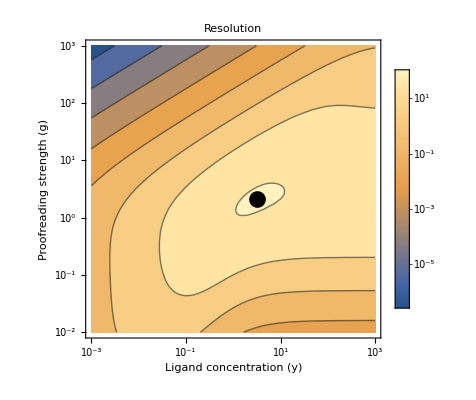

```mathematica
FigS1EFrameTicks={{Table[{i,Superscript[10,i]},{i,-2,3}],None},{Table[{i,Superscript[10,i]},{i,-3,3}],None}};
FigS1EtickSFs={1,0.573,0.59,0.67,0.43};
FigS1Eticks={#[[1]],Style[#[[2]],{Black,FontSize->18}]}&/@Table[{i,Superscript[10,i]},{i,-7,2,2}];
FigS1Eticks=Table[{FigS1EtickSFs[[i]]*FigS1Eticks[[i,1]],FigS1Eticks[[i,2]]},{i,1,Length[FigS1Eticks]}];
FigS1EbarLegend=Overlay[{BarLegend[{"M10DefaultDensityGradient",{-3.75,1}},LegendMarkerSize->240,LegendMargins->{{0,0},{20,0}},Ticks->FigS1Eticks,LabelStyle->Black],
BarLegend[{"M10DefaultDensityGradient",{-3.75,1}},8,LegendMarkerSize->250,LegendMargins->{{0,0},{20,0}},Ticks->None]}];

FigS1E=ContourPlot[Log10[KPR1BPk]/.xgParams,{ctest,-3,3},{gtest,-2,3},
Epilog->{PointSize[0.03],{Black,Point[{Log10[3.2],Log10[2.1]}]}},FrameLabel->{"Ligand concentration  (y)","Proofreading strength  (g)"},PlotLegends->FigS1EbarLegend,PlotLabel->"Resolution",LabelStyle->{Black,FontSize->18},TicksStyle->Black,FrameTicks->FigS1EFrameTicks,PlotRange->All]
```

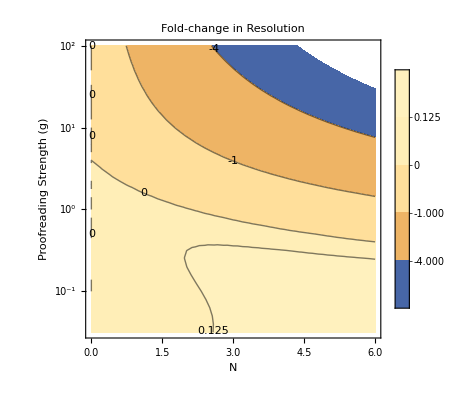

```mathematica
estimateParams={kon->1,kp->1,t->100,koff->10^gtest,δ->0.1,c->10^ctest,kf->1};
data=Flatten[Table[{NTEST,GTEST,Log10[BPMetric[koff,ΣkN]/BPMetric[koff,Σk0]]}/.estimateParams/.{ctest->-1,gtest->GTEST,Ns->NTEST},{GTEST,-1.5,2,0.1},{NTEST,0,6,0.2}],1];

plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)"},
PlotLegends->Automatic,
PlotLabel->"Fold-change in\nResolution",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-2,3}],None},{Automatic,None}},
Contours->Evaluate@Join[Table[i,{i,0.5,0,-0.125}],Table[-i^2,{i,1,7}]],
ContourLabels->True};
FigS2=ListContourPlot[data,Evaluate@plotOptions]
```

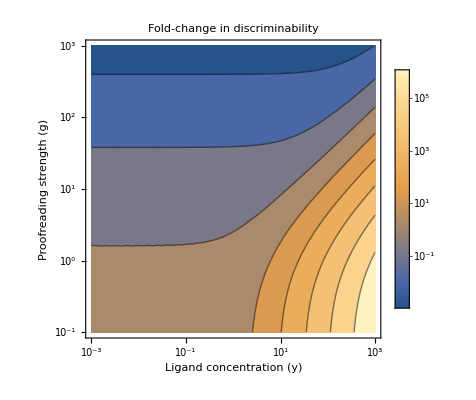

```mathematica
FigS1CtickSFs={1.6,0.55,0.89,0.97};
FigS1Cticks={#[[1]],Style[#[[2]],{Black,FontSize->18}]}&/@Table[{i,Superscript[10,i]},{i,-1,5,2}];
FigS1Cticks=Table[{FigS1CtickSFs[[i]]*FigS1Cticks[[i,1]],FigS1Cticks[[i,2]]},{i,1,Length[FigS1Cticks]}];
FigS1CbarLegend=Overlay[{BarLegend[{"M10DefaultDensityGradient",{-3.75,6}},LegendMarkerSize->200,LegendMargins->{{0,0},{20,0}},Ticks->FigS1Cticks,LabelStyle->Black],
BarLegend[{"M10DefaultDensityGradient",{-3.75,6}},8,LegendMarkerSize->200,LegendMargins->{{0,0},{20,0}},Ticks->None]}];

FigS1C=ContourPlot[Log10[KPR1BPk/KPR0BPk]/.xgParams,{ctest,-3,3},{gtest,-1,3},FrameLabel->{"Ligand concentration  (y)","Proofreading strength  (g)"},PlotLegends->FigS1CbarLegend,PlotLabel->"Fold-change in\nResolution",LabelStyle->{Black,FontSize->18},TicksStyle->Black,FrameTicks->xgTicks]
```

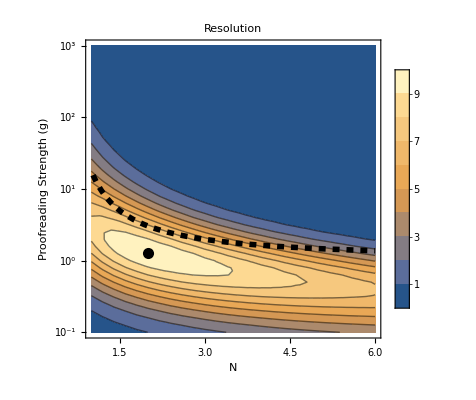

```mathematica
data=Flatten[Table[{NTEST,GTEST,BPMetric[koff,ΣkN]}/.xgParams/.{ctest->2,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.1},{NTEST,1,6,0.2}],1];
EpilogPoint=MaximalBy[data,Last][[1]];
plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)"},
PlotLegends->Automatic,
PlotLabel->"Resolution",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Automatic,None}}};
FigS1ResAtHighC=Show[
ListContourPlot[data,Evaluate@plotOptions,
Epilog->{PointSize[0.02],{Black,Point[{EpilogPoint[[1]],EpilogPoint[[2]]}]}}],
Plot[(1-2^(1/Ns))/(-1+0.1 2^(1/Ns)),{Ns,1.03,6},PlotStyle->{Black,Dashed,Thickness[0.01]}]
]
```

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["FigS1RatHighC.pdf",FigS1ResAtHighC];
```

## Response to Reviewers

### Reviewer 1

```mathematica
ηN/η0/.contractParams/.koff->1
```

(1+1/g)^Ns (1/g+δ)^-Ns

```mathematica
Solve[(1+1/g)^Ns (1/g+δ)^-Ns==ηtarg,g]
```

{{g→(1-ηtarg^(1/Ns))/(-1+δ ηtarg^(1/Ns))}}

```mathematica
ηN/.contractParams
```

((koff+koff/g)^Ns (koff+koff x) (koff/g+koff δ)^-Ns)/(koff x+koff δ)

```mathematica
Solve[((koff+koff/g)^Ns (koff+koff x) (koff/g+koff δ)^-Ns)/(koff x+koff δ)==η,g]//Simplify
```

{{g→(-((1+x)/(x+δ))^(1/Ns)+η^(1/Ns))/(((1+x)/(x+δ))^(1/Ns)-δ η^(1/Ns))}}

```mathematica
μN/.contractParams
```

((1+g)^-Ns kp t x)/(1+x)

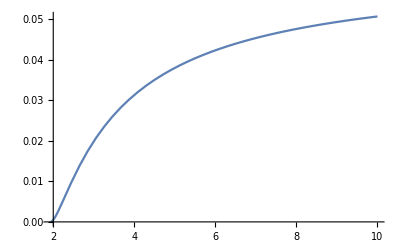

```mathematica
Plot[((1+g)^-Ns x)/(1+x)/.{g->(-((1+x)/(x+ζ))^(1/Ns)+η^(1/Ns))/(((1+x)/(x+ζ))^(1/Ns)-ζ η^(1/Ns))}/.ζ->0.5/.η->4/.x->10,{Ns,0,10},PlotRange->All]
```

```mathematica
Solve[-1+ζ η^(1/Ns)==0,Ns]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Ns→Log[η]/Log[1/ζ]}}

```mathematica
Log[1/ζ,η]
```

Log[η]/Log[1/ζ]

Power::infy: Infinite expression 1/0. encountered.

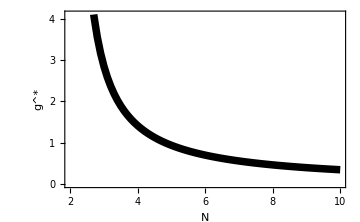
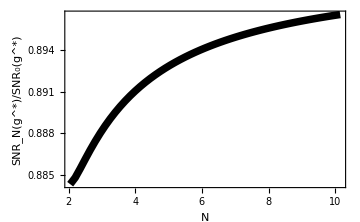
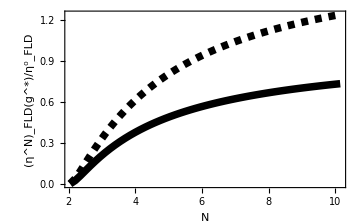

```mathematica
SNRn=μN/ΣN/.contractParams;
SNR0=μ0/Σ0/.contractParams;
test={x->0.1,ζ->0.5,koff->1,kp->1,ηtarg->4};
pt={Ntest,(1-ηtarg^(1/Ntest))/(-1+ζ ηtarg^(1/Ntest))/.test};
l1=Table[pt,{Ntest,2,10,0.1}];
g1=ListPlot[l1,Joined->True,PlotRange->{{2,Automatic},Automatic},Frame->{{True,False},{True,False}},FrameLabel->{"N","g^*"},LabelStyle->{Black,FontSize->16},ImageSize->Medium,PlotStyle->{Black,Thickness[0.015]}];
pt={Ntest,SNRn/SNR0/.Ns->Ntest/.test/.{g->(1-ηtarg^(1/Ntest))/(-1+ζ ηtarg^(1/Ntest))/.test}};
l2=Table[pt,{Ntest,1.15,10.15,0.15}];
g2=ListPlot[l2,Joined->True,PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"N","SNR_N(g^*)/SNR_0(g^*)"},LabelStyle->{Black,FontSize->16},ImageSize->Medium,PlotStyle->{Black,Thickness[0.015]}];

pt={Ntest,KPRNBPk/KPR0BPk/.contractParams/.{δ->ζ}/.Ns->Ntest/.test/.{g->(1-ηtarg^(1/Ntest))/(-1+ζ ηtarg^(1/Ntest))/.test}};
l3=Table[pt,{Ntest,1.15,10.15,0.15}];

test={x->1,ζ->0.5,koff->1,kp->1,ηtarg->4};
pt={Ntest,KPRNBPk/KPR0BPk/.contractParams/.{δ->ζ}/.Ns->Ntest/.test/.{g->(1-ηtarg^(1/Ntest))/(-1+ζ ηtarg^(1/Ntest))/.test}};
l4=Table[pt,{Ntest,1.15,10.15,0.15}];

g3=ListPlot[{l3,l4},Joined->True,PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"N","(η^N)_FLD(g^*)/(η^0)_FLD"},LabelStyle->{Black,FontSize->16},ImageSize->Medium,PlotStyle->{{Black,Thickness[0.015]},{Black,Thickness[0.015],Dashed}}];

FigS3=Row[{g1,,g2, , g3}]
```

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["FigS3.pdf",FigS3];
```

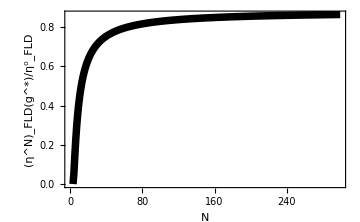

```mathematica
test={x->1,ζ->0.5,koff->1,kp->1,ηtarg->8};
ListPlot[Table[{Ntest,KPRNBPk/KPR0BPk/.contractParams/.{δ->ζ}/.Ns->Ntest/.test/.{g->(1-ηtarg^(1/Ntest))/(-1+ζ ηtarg^(1/Ntest))/.test}},{Ntest,1.15,300}],Joined->True,PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"N","(η^N)_FLD(g^*)/(η^0)_FLD"},LabelStyle->{Black,FontSize->16},ImageSize->Medium,PlotStyle->{Black,Thickness[0.015]}]
```

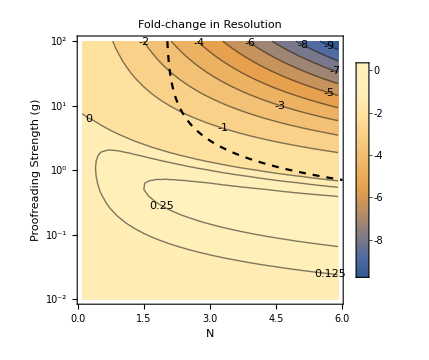

```mathematica
estimateParams={kon->1,kp->1,t->100,koff->1,δ->0.5,c->10^ctest,kf->10^-gtest};
NMAX=6;
data=Flatten[Table[{NTEST,GTEST,Log10[BPMetric[koff,ΣkN]/BPMetric[koff,Σk0]]}/.estimateParams/.{ctest->0,gtest->GTEST,Ns->NTEST},{GTEST,-2,2,0.1},{NTEST,0.1,NMAX,0.2}],1];

plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)"},
PlotLegends->Automatic,
PlotLabel->"Fold-change in\nResolution",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-2,3}],None},{Automatic,None}},
Contours->Evaluate@Join[Table[i,{i,1.75,0,-0.125}],Table[-i,{i,1,15}]],
ContourLabels->True,ImageSize->Medium,PlotRange->{-2 NMAX,1}};
FigS1G=ListContourPlot[data,Evaluate@plotOptions];

contour=Plot[Log10[(1-4^(1/Ntest))/(-1+0.5 4^(1/Ntest))],{Ntest,1,NMAX},PlotRange->{{0,NMAX},{-2,2}},PlotStyle->{Black,Dashed,Thickness->0.01},AspectRatio->1,ImageSize->Medium];
FigS1G=Show[FigS1G,contour]
```

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["FigS1G.pdf",FigS1G];
```

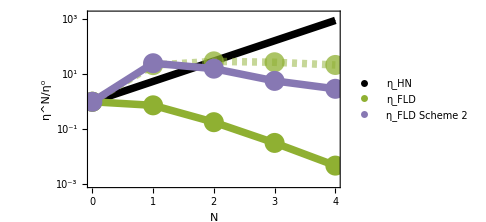
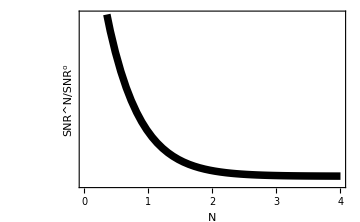

```mathematica
testpoint={ctest->1,gtest->1};
testpoint2={ctest->1,gtest->0};
yticks=Table[{2.301i,Superscript[10,i]},{i,-3,3}];
p1=ListLogPlot[Table[{Ns,ηN/η0}/.xgParams/.testpoint,{Ns,0,4,1}],Frame->{{True,False},{True,False}},FrameLabel->{"N","η^N/η^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{PointSize[0.00],Black},FrameTicks->{{yticks,None},{{0,1,2,3,4},None}},PlotRange->{Automatic,{0.001,1500}}];
p2=LogPlot[ηN/η0/.xgParams/.testpoint,{Ns,0,4},PlotStyle->{Thickness[0.015],Black}];



BPKscale={{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk}}/.xgParams/.testpoint;
BPKscale2={{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk}}/.xgParams/.testpoint2;
FLDReviewer2ModelSim={{0,1.00},{1,25.24},{2,16.05},{3,5.75},{4,2.96}};

g1=Legended[
Show[p1,p2,

ListLogPlot[BPKscale,PlotStyle->{cmap[[3]],PointSize[0.04]}],
ListLogPlot[BPKscale,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015]}],

ListLogPlot[BPKscale2,PlotStyle->{cmap[[3]],PointSize[0.04],Opacity[0.75]}],
ListLogPlot[BPKscale2,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015],Dashing[0.01],Opacity[0.5]}],


ListLogPlot[FLDReviewer2ModelSim,PlotStyle->{cmap[[5]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSim,Joined->True,PlotStyle->{cmap[[5]],Thickness[0.015]}],

ImageSize->Medium
],
PointLegend[{Black,cmap[[3]],cmap[[5]]},{"η_HN","η_FLD","η_FLD Scheme 2"},LegendMarkerSize->25]];
g2=LogPlot[SNRn/SNR0/.expandParams/.xgParams/.Ns->Ntest/.testpoint,{Ntest,0,4},
Frame->{{True,False},{True,False}},FrameLabel->{"N","SNR^N/SNR^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{Black,Thickness[0.015]},FrameTicks->{{Automatic,None},{{0,1,2,3,4},None}},ImageSize->Medium];
Row[{g1,g2}]
```

```mathematica
CF1=Log10[(μN/.koff->ζ koff)/μN+λ (μN/(√ΣN)/.koff->ζ koff)];
CF2=Log10[μN/(μN/.koff->ζ koff)+λ ((μN/(√ΣN))^-1/.koff->ζ koff)];
```

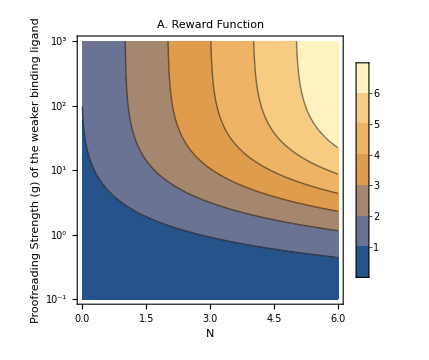
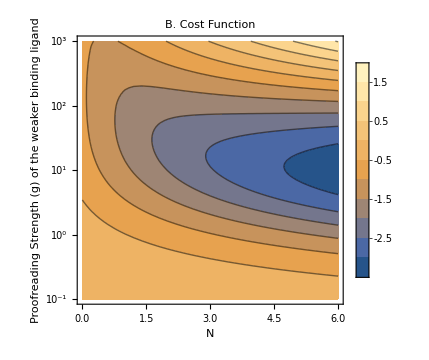

```mathematica
estimateParams={kon->1,kp->1,t->100,koff->10^gtest,c->10^ctest,kf->1,ζ->0.1,λ->10^-1};
plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)\n of  the weaker binding ligand"},
PlotLegends->Automatic,
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Automatic,None}},
ImageSize->Medium};

data1=Flatten[Table[{NTEST,GTEST,CF1}/.expandParams/.estimateParams/.{ctest->0,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.05},{NTEST,0,6,0.2}],1];
S4A=ListContourPlot[data1,PlotLabel->"A. Reward Function",Evaluate@plotOptions];


data2=Flatten[Table[{NTEST,GTEST,CF2}/.expandParams/.estimateParams/.{ctest->0,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.05},{NTEST,0,6,0.2}],1];
S4B=ListContourPlot[data2,PlotLabel->"B. Cost Function",Evaluate@plotOptions];
FigureS4=Row[{S4A,S4B}]
```

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["FigS4.pdf",FigureS4]
```

FigS4.pdf

#### Deriving MFPT vs N

To calculate the first passage time, follow “Bel, Munsky, & Nemenman (2010)”: make the terminal state an absorbing state and convert the Master equation to algebraic equations using a Laplace transform.

The Master equation for this system can be written in the form dp/dt=A·p which takes the form p(t=0)=(s-A)P(s) after the Laplace transform p(t)→P(s)

Since p_N is the cumulative probability that the system has reached the absorbing state, the first passage time probability density, f(t)=dp_N/dt, can be written in the Laplace domain as:
F(s)=(∫_0)^∞e^-st dp_N/dt dt=e^-st p_N(|^∞)_(t=0)+s(∫_0)^∞e^-st p_N dt
F(s)=sP_N(s)

All uncentered moments of the first passage time distribution are derived as:
T^(m)=(∫_0)^∞t^m f(t)dt
          =(d/ds)^m(-1)^m(∫_0)^∞f(t)e^-st dt|_(s=0)
 =(-1)^m(d^m F(s))/ds^m|_(s=0)

Therefore, the mean and squared coefficient of variation CV^2=σ^2/μ^2 are computed as:
μ=T^(1)=(-dF(s))/ds|_(s=0)
CV^2=(T^(2)-(T^(1))^2)/((T^(1))^2)=((d^2 F(s))/ds^2-((dF(s))/ds)^2)/((dF(s))/ds)^2|_(s=0)

```mathematica
Aij={{-kon c,0},{kon c,0}};
Block[{i},
eqs={};
For[i=1,i≤2,i++,
AppendTo[eqs,(s {P0,P1}-Aij.{P0,P1})[[i]]==KroneckerDelta[i,1]]
]
]
sol=Solve[eqs,{P0,P1}];
F=s(P0/.sol)[[1]];
-D[F,s]//Simplify;
MFPT0=%/.s->0
```

-1/(c kon)

```mathematica
Aij={{-kon c,koff,0},{kon c,-koff-kf,0},{0,kf,0}};
Block[{i},
eqs={};
For[i=1,i≤3,i++,
AppendTo[eqs,(s {P0,P1,P2}-Aij.{P0,P1,P2})[[i]]==KroneckerDelta[i,1]]
]
]
sol=Solve[eqs,{P0,P1,P2}];
F=s(P2/.sol)[[1]];
-D[F,s]//Simplify;
MFPT1=%/.s->0
```

(kf+koff+c kon)/(c kf kon)

```mathematica
Aij={{-kon c,koff,koff,0},{kon c,-koff-kf,0,0},{0,kf,-kf,0},{0,0,kf,0}};
Block[{i},
eqs={};
For[i=1,i≤4,i++,
AppendTo[eqs,(s {P0,P1,P2,P3}-Aij.{P0,P1,P2,P3})[[i]]==KroneckerDelta[i,1]]
]
]
Print[eqs];
sol=Solve[eqs,{P0,P1,P2,P3}];
F=s(P3/.sol)[[1]];
-D[F,s]//Simplify;
MFPT2=%/.s->0
```

{c kon P0-koff P1-koff P2+P0 s==1,-c kon P0-(-kf-koff) P1+P1 s==0,-kf P1+kf P2+P2 s==0,-kf P2+P3 s==0}

(kf^2 (kf^2+kf (koff+2 c kon)))/(c (kf^2-kf koff)^2 kon)

```mathematica
Aij={{-kon c,koff,koff,koff,0},{kon c,-koff-kf,0,0,0},{0,kf,-kf,0,0},{0,0,kf,-kf,0},{0,0,0,kf,0}};
Block[{i},
eqs={};
For[i=1,i≤5,i++,
AppendTo[eqs,(s {P0,P1,P2,P3,P4}-Aij.{P0,P1,P2,P3,P4})[[i]]==KroneckerDelta[i,1]]
]
]
sol=Solve[eqs,{P0,P1,P2,P3,P4}];
F=s(P4/.sol)[[1]];
-D[F,s]//Simplify;
MFPT3=%/.s->0
```

(kf^3 (kf^3-c kf koff kon+kf^2 (koff+3 c kon)))/(c (kf^3-2 kf^2 koff)^2 kon)

```mathematica
Aij={{-kon c,koff,koff,koff,koff,0},{kon c,-koff-kf,0,0,0,0},{0,kf,-kf,0,0,0},{0,0,kf,-kf,0,0},{0,0,0,kf,-kf,0},{0,0,0,0,kf,0}};
Block[{i},
eqs={};
For[i=1,i≤6,i++,
AppendTo[eqs,(s {P0,P1,P2,P3,P4,P5}-Aij.{P0,P1,P2,P3,P4,P5})[[i]]==KroneckerDelta[i,1]]
]
]
sol=Solve[eqs,{P0,P1,P2,P3,P4,P5}];
F=s(P5/.sol)[[1]];
-D[F,s]//Simplify;
MFPT4=%/.s->0
```

(kf^4 (kf^4-3 c kf^2 koff kon+kf^3 (koff+4 c kon)))/(c (kf^4-3 kf^3 koff)^2 kon)

```mathematica
Aij={{-kon c,koff,koff,koff,koff,koff,0},{kon c,-koff-kf,0,0,0,0,0},{0,kf,-kf,0,0,0,0},{0,0,kf,-kf,0,0,0},{0,0,0,kf,-kf,0,0},{0,0,0,0,kf,-kf,0},{0,0,0,0,0,kf,0}};
Block[{i},
eqs={};
For[i=1,i≤7,i++,
AppendTo[eqs,(s {P0,P1,P2,P3,P4,P5,P6}-Aij.{P0,P1,P2,P3,P4,P5,P6})[[i]]==KroneckerDelta[i,1]]
]
]
sol=Solve[eqs,{P0,P1,P2,P3,P4,P5,P6}];
F=s(P6/.sol)[[1]];
-D[F,s]//Simplify;
MFPT5=%/.s->0
```

(kf^5 (kf^5-6 c kf^3 koff kon+kf^4 (koff+5 c kon)))/(c (kf^5-4 kf^4 koff)^2 kon)

```mathematica
Aij={{-kon c,koff,koff,koff,koff,koff,koff,0},{kon c,-koff-kf,0,0,0,0,0,0},{0,kf,-kf,0,0,0,0,0},{0,0,kf,-kf,0,0,0,0},{0,0,0,kf,-kf,0,0,0},{0,0,0,0,kf,-kf,0,0},{0,0,0,0,0,kf,-kf,0},{0,0,0,0,0,0,kf,0}};
Block[{i},
eqs={};
For[i=1,i≤8,i++,
AppendTo[eqs,(s {P0,P1,P2,P3,P4,P5,P6,P7}-Aij.{P0,P1,P2,P3,P4,P5,P6,P7})[[i]]==KroneckerDelta[i,1]]
]
]
sol=Solve[eqs,{P0,P1,P2,P3,P4,P5,P6,P7}];
F=s(P7/.sol)[[1]];
-D[F,s]//Simplify;
MFPT6=%/.s->0
```

(kf^6 (kf^6-10 c kf^4 koff kon+kf^5 (koff+6 c kon)))/(c (kf^6-5 kf^5 koff)^2 kon)

```mathematica
Aij={{-kon c,koff,koff,koff,koff,koff,koff,koff,0},{kon c,-koff-kf,0,0,0,0,0,0,0},{0,kf,-kf,0,0,0,0,0,0},{0,0,kf,-kf,0,0,0,0,0},{0,0,0,kf,-kf,0,0,0,0},{0,0,0,0,kf,-kf,0,0,0},{0,0,0,0,0,kf,-kf,0,0},{0,0,0,0,0,0,kf,-kf,0},{0,0,0,0,0,0,0,kf,0}};
Block[{i},
eqs={};
For[i=1,i≤9,i++,
AppendTo[eqs,(s {P0,P1,P2,P3,P4,P5,P6,P7,P8}-Aij.{P0,P1,P2,P3,P4,P5,P6,P7,P8})[[i]]==KroneckerDelta[i,1]]
]
]
sol=Solve[eqs,{P0,P1,P2,P3,P4,P5,P6,P7,P8}];
F=s(P8/.sol)[[1]];
-D[F,s]//Simplify;
MFPT7=%/.s->0
```

(kf^7 (kf^7-15 c kf^5 koff kon+kf^6 (koff+7 c kon)))/(c (kf^7-6 kf^6 koff)^2 kon)

```mathematica
MFPTN=(kf^Ns(kf^Ns-((Ns-2)(Ns-1))/2 c kf^(Ns-2) koff kon+kf^(Ns-1)(koff+Ns c kon)))/(c(kf^Ns-(Ns-1)kf^(Ns-1)koff)^2 kon);
genTest=Table[MFPTN,{Ns,0,7}]
MFPT0-genTest[[1]]
MFPT1-genTest[[2]]//Simplify
MFPT2-genTest[[3]]
MFPT3-genTest[[4]]
MFPT4-genTest[[5]]
MFPT5-genTest[[6]]
MFPT6-genTest[[7]]
MFPT7-genTest[[8]]
```

{(1+koff/kf-(c koff kon)/kf^2)/(c (1+koff/kf)^2 kon),(kf+koff+c kon)/(c kf kon),(kf^2 (kf^2+kf (koff+2 c kon)))/(c (kf^2-kf koff)^2 kon),(kf^3 (kf^3-c kf koff kon+kf^2 (koff+3 c kon)))/(c (kf^3-2 kf^2 koff)^2 kon),(kf^4 (kf^4-3 c kf^2 koff kon+kf^3 (koff+4 c kon)))/(c (kf^4-3 kf^3 koff)^2 kon),(kf^5 (kf^5-6 c kf^3 koff kon+kf^4 (koff+5 c kon)))/(c (kf^5-4 kf^4 koff)^2 kon),(kf^6 (kf^6-10 c kf^4 koff kon+kf^5 (koff+6 c kon)))/(c (kf^6-5 kf^5 koff)^2 kon),(kf^7 (kf^7-15 c kf^5 koff kon+kf^6 (koff+7 c kon)))/(c (kf^7-6 kf^6 koff)^2 kon)}

1/(c kon)-(1+koff/kf-(c koff kon)/kf^2)/(c (1+koff/kf)^2 kon)

0

0

0

«4 more identical outputs»

So general formula is good for N≥ 2

#### Plotting MFPT vs N

```mathematica
test={kon->1,c->1,ζ->0.5,koff->1,kp->1,ηtarg->4};
l5=Join[{MFPT0,MFPT1},Table[MFPTN,{Ns,2,10,0.5}]];
l6=Table[{kf->Min[10^8,((1-ηtarg^(1/Ntest))/(-1+ζ ηtarg^(1/Ntest)))^-1]}/.test,{Ntest,0,10}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ηtarg^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ηtarg^ComplexInfinity encountered.

{{kf→Indeterminate},{kf→-0.333333},{kf→0.},{kf→0.351207},{kf→0.707107},{kf→1.06491},{kf→1.42366},{kf→1.78296},{kf→2.14261},{kf→2.50248},{kf→2.86251}}

Part::partw: Part 12 of {{kf→Indeterminate},{kf→-0.333333},{kf→0.},{kf→0.351207},{kf→0.707107},{kf→1.06491},{kf→1.42366},{kf→1.78296},{kf→2.14261},{kf→2.50248},{kf→2.86251}} does not exist.

ReplaceAll::reps: {{{kf→Indeterminate},{kf→-0.333333},{kf→0.},{kf→0.351207},{kf→0.707107},{kf→1.06491},{kf→1.42366},{kf→1.78296},{kf→2.14261},{kf→2.50248},{kf→2.86251}}⟦12⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 12 of {{kf→Indeterminate},{kf→-0.333333},{kf→0.},{kf→0.351207},{kf→0.707107},{kf→1.06491},{kf→1.42366},{kf→1.78296},{kf→2.14261},{kf→2.50248},{kf→2.86251}} does not exist.

ReplaceAll::reps: {{{kf→Indeterminate},{kf→-0.333333},{kf→0.},{kf→0.351207},{kf→0.707107},{kf→1.06491},{kf→1.42366},{kf→1.78296},{kf→2.14261},{kf→2.50248},{kf→2.86251}}⟦12⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 13 of {{kf→Indeterminate},{kf→-0.333333},{kf→0.},{kf→0.351207},{kf→0.707107},{kf→1.06491},{kf→1.42366},{kf→1.78296},{kf→2.14261},{kf→2.50248},{kf→2.86251}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{{kf→Indeterminate},{kf→-0.333333},{kf→0.},{kf→0.351207},{kf→0.707107},{kf→1.06491},{kf→1.42366},{kf→1.78296},{kf→2.14261},{kf→2.50248},{kf→2.86251}}⟦13⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

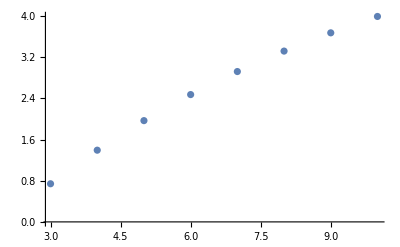

```mathematica
ListPlot[Table[{i-1,l5[[i]]/.l6[[i]]/.test},{i,4,Length[l5]}]]
```

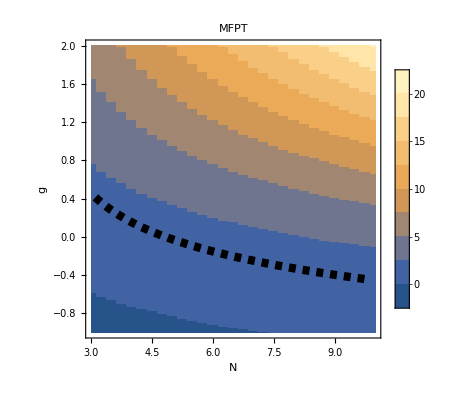

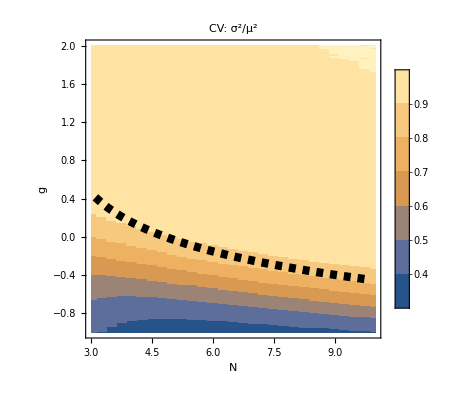

```mathematica
test={x->1,koff->1,kp->1};
BelMFPT=1/(k ψ)((1+ψ)^Ns-1)/.{k->kf,ψ->koff/kf};
CVcompletiontime=((1+ψ)^(2 Ns)-2 ψ Ns(1+ψ)^(Ns-1)-1)/((1+ψ)^(2 Ns)-2(1+ψ)^Ns+1)/.{k->kf,ψ->koff/kf};
Show[
ListContourPlot[Flatten[Table[{i,GTEST,Log10@BelMFPT/.contractParams/.Ns->i/.test/.g->10^GTEST},{i,3,10,0.25},{GTEST,-1,2,0.01}],1],PlotLegends->Automatic,PlotRange->All,PlotLabel->"MFPT",FrameLabel->{"N","g"},FrameTicksStyle->{Black,FontSize->16},LabelStyle->{Black,FontSize->16},FrameTicks->{{Automatic,None},{Table[{KFTEST,Superscript[10,KFTEST]},{KFTEST,-1,1,0.5}]},None},InterpolationOrder->0],
ListPlot[Table[{Ntest,Log10[((1-ηtarg^(1/Ntest))/(-1+ζ ηtarg^(1/Ntest)))]/.test/.{ζ->0.5,ηtarg->4}},{Ntest,3.1,9.9,0.1}],Joined->True,PlotStyle->{Black,Dashed,Thickness[0.015]}]
]

Show[
ListContourPlot[Flatten[Table[{i,GTEST,CVcompletiontime/.contractParams/.Ns->i/.test/.g->10^GTEST},{i,3,10,0.25},{GTEST,-1,2,0.01}],1],PlotLegends->Automatic,PlotRange->All,PlotLabel->"CV: σ^2/μ^2",FrameLabel->{"N","g"},FrameTicksStyle->{Black,FontSize->16},LabelStyle->{Black,FontSize->16},FrameTicks->{{Automatic,None},{Table[{KFTEST,Superscript[10,KFTEST]},{KFTEST,-1,1,0.5}]},None},InterpolationOrder->0],
ListPlot[Table[{Ntest,Log10[((1-ηtarg^(1/Ntest))/(-1+ζ ηtarg^(1/Ntest)))]/.test/.{ζ->0.5,ηtarg->4}},{Ntest,3.1,9.9,0.1}],Joined->True,PlotStyle->{Black,Dashed,Thickness[0.015]}]
]
```

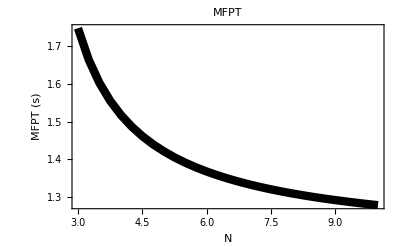

```mathematica
ListPlot[Table[{i,Log10@BelMFPT/.contractParams/.Ns->i/.test/.g->((1-4^(1/i))/(-1+0.5 4^(1/i)))},{i,3,10,0.25}],
Joined->True,PlotStyle->{Black,Thickness[0.015]},PlotRange->All,PlotLabel->"MFPT",Frame->{{True,False},{True,False}},FrameLabel->{"N","MFPT (s)"},FrameTicksStyle->{Black,FontSize->16},LabelStyle->{Black,FontSize->16}]
```

```mathematica
λ=kf/(s+kf+koff);
C1=1/(s+kf-koff((1-λ^Ns)/(1-λ)-1));
fs=kf C1 λ^(Ns-1);
```

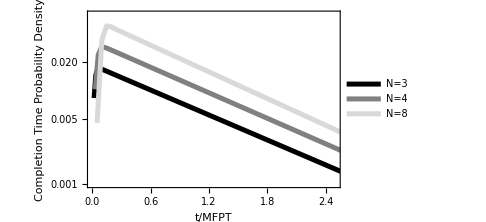

FigS3D.pdf

```mathematica
lightToDark[n_,c_:Red]:=Blend[{{0,White},{n/2,c},{n+3,Black}},#]&/@Range[n]
functions={
Table[{t/BelMFPT/.{koff->1,kf->((1-4^(1/3))/(-1+0.5 4^(1/3)))^-1,Ns->3},InverseLaplaceTransform[fs,s,t]/.{koff->1,kf->((1-4^(1/3))/(-1+0.5 4^(1/3)))^-1,Ns->3}},{t,0,200}],
Table[{t/BelMFPT/.{koff->1,kf->((1-4^(1/4))/(-1+0.5 4^(1/4)))^-1,Ns->4},Re@InverseLaplaceTransform[fs,s,t]/.{koff->1,kf->((1-4^(1/4))/(-1+0.5 4^(1/4)))^-1,Ns->4}},{t,0,100}],
Table[{t/BelMFPT/.{koff->1,kf->((1-4^(1/8))/(-1+0.5 4^(1/8)))^-1,Ns->8},Re@InverseLaplaceTransform[fs,s,t]/.{koff->1,kf->((1-4^(1/8))/(-1+0.5 4^(1/8)))^-1,Ns->8}},{t,0,100}]};

cmap2={Black,Gray,LightGray};

FigS3D=ListLogPlot[functions,
Joined->True,
PlotRange->{{0,2.5},{0.001,0.065}},
PlotStyle->Partition[Riffle[cmap2,Thickness[0.01],{2,-1,2}],2],
PlotLegends->{"N=3","N=4","N=8"},
LabelStyle->{Black,FontSize->12},
Frame->{{True,False},{True,False}},
FrameStyle->Black,
TicksStyle->{Black,FontSize->16},
FrameLabel->{"t/MFPT","Completion Time\n Probability Density"},
ImageSize->Medium]
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["FigS3D.pdf",FigS3D]
```

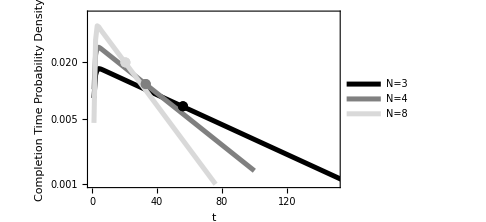

```mathematica
lightToDark[n_,c_:Red]:=Blend[{{0,White},{n/2,c},{n+3,Black}},#]&/@Range[n]
f2={
Table[{t,InverseLaplaceTransform[fs,s,t]/.{koff->1,kf->((1-4^(1/3))/(-1+0.5 4^(1/3)))^-1,Ns->3}},{t,0,200}],
Table[{t,Re@InverseLaplaceTransform[fs,s,t]/.{koff->1,kf->((1-4^(1/4))/(-1+0.5 4^(1/4)))^-1,Ns->4}},{t,0,100}],
Table[{t,Re@InverseLaplaceTransform[fs,s,t]/.{koff->1,kf->((1-4^(1/8))/(-1+0.5 4^(1/8)))^-1,Ns->8}},{t,0,100}]};

cmap2={Black,Gray,LightGray};
Show[
ListLogPlot[f2,
Joined->True,
PlotRange->{{0,150},{0.001,0.065}},
PlotStyle->Partition[Riffle[cmap2,Thickness[0.01],{2,-1,2}],2],
PlotLegends->{"N=3","N=4","N=8"},
LabelStyle->{Black,FontSize->12},
Frame->{{True,False},{True,False}},
FrameStyle->Black,
TicksStyle->{Black,FontSize->16},
FrameLabel->{"t","Completion Time\n Probability Density"},
ImageSize->Medium],

ListLogPlot[{{BelMFPT/.{koff->1,kf->((1-4^(1/3))/(-1+0.5 4^(1/3)))^-1,Ns->3},0.0068}},PlotStyle->{Black,PointSize[0.02]}],
ListLogPlot[{{BelMFPT/.{koff->1,kf->((1-4^(1/4))/(-1+0.5 4^(1/4)))^-1,Ns->4},0.01175}},PlotStyle->{Gray,PointSize[0.02]}],
ListLogPlot[{{BelMFPT/.{koff->1,kf->((1-4^(1/8))/(-1+0.5 4^(1/8)))^-1,Ns->8},0.02}},PlotStyle->{LightGray,PointSize[0.02]}]
]
```

### Reviewer 2

#### Mutual Information

Entropy: H[x]= - Integrate[P(x) Log[P(x)], dx]
Conditional entropy: H[x|y]= - Integrate[P(y) Integrate[P(x|y) Log[P(x|y)], dx], dy]


Prior on koff will be log-normal centered at koff=1.
Prior on n will be exponential ~ λ e^(-λ n) where λ=(kp*t)^-1
MI = H(koff) - H(koff|n)
and H(koff)= - Integrate[P[koff] Log[P[koff]],{koff,0,1000}]
and H(koff|n)= - Integrate[P[koff,n] Log[P[koff,n]/P[n]],{n,0,1000}, {koff,0,1000}]
Define: P[koff,n]=P[n|koff]P[koff]

```mathematica
Pkoff[koff_,μ_:0,σ_:1]:=1/(σ koff √(2π))E^(-1/2((Log[koff]-μ)/σ)^2);(*Log-normal PDF*)
(*Pkoff[koff_]:=10 E^(-10koff);Exponential PDF*)
```

```mathematica
Pnlk[n_,koff_,Ns_]:=Module[{c=1,kf=1,kon=1,kp=1,t=100,σn,μ},
μ=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff));
σn=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff))+(2 c (1+koff/kf)^-Ns kon kp^2 t)/(koff (koff+c kon))-(2 c^2 (1+koff/kf)^(-1-2 Ns) kon^2 kp^2 (2+(c kon)/koff+(koff (2+(c kon)/koff+Ns+(c kon Ns)/koff))/kf) t)/(koff^3 (1+(c kon)/koff)^3);
1/(√(2π σn))E^(-1/2((n-μ)/(√σn))^2)];
MIlist={};
MethodList={"GlobalAdaptive","LocalAdaptive","GlobalAdaptive","GlobalAdaptive","GlobalAdaptive","GlobalAdaptive","GlobalAdaptive","GlobalAdaptive"};
For[i=0,i<8,i++,
Print[i];
HNK=-NIntegrate[Pkoff[k,1,2]Pnlk[n,k,i] Log2[Pnlk[n,k,i]],{k,0,Infinity},{n,0,Infinity},Method->MethodList[[i+1]]];
Pn[n_]:=NIntegrate[Pnlk[n,k,i]Pkoff[k,1,2],{k,0,Infinity}];
HN=-NIntegrate[Pn[n]Log2[Pn[n]],{n,0,Infinity}];
AppendTo[MIlist,HN-HNK];
]
MIlist
```

0

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumr: The integrand (ⅇ^(-(«1»+n)^2/(2 («1»))-1/8 (-1+Log[k])^2))/(4 k √(100/((1+1/k) k)+200/(k (1+k))-(200 (2+1/k+(2+Power[«2»]) k))/((1+1/k)^3 k^3 (1+k))) π) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1

2

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

4

5

6

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in n near {k,n} = {39692.3,1.11022×10^-15}. NIntegrate obtained 0.61615+3.25917×10^-173 ⅈ and 7.0512×10^-7 for the integral and error estimates.

7

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in n near {k,n} = {10390.,1.11022×10^-15}. NIntegrate obtained 1.26498+3.21157×10^-173 ⅈ and 7.65987×10^-6 for the integral and error estimates.

{2.10104+2.00759×10^-173 ⅈ,1.93999,1.78019,1.74136+3.1361×10^-173 ⅈ,1.71736+3.23467×10^-173 ⅈ,1.71466+3.47904×10^-173 ⅈ,1.72376,1.73962}

```mathematica
Pnlk[n_,koff_,Ns_]:=Module[{c=1,kf=10,kon=1,kp=1,t=100,σn,μ},
μ=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff));
σn=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff))+(2 c (1+koff/kf)^-Ns kon kp^2 t)/(koff (koff+c kon))-(2 c^2 (1+koff/kf)^(-1-2 Ns) kon^2 kp^2 (2+(c kon)/koff+(koff (2+(c kon)/koff+Ns+(c kon Ns)/koff))/kf) t)/(koff^3 (1+(c kon)/koff)^3);
1/(√(2π σn))E^(-1/2((n-μ)/(√σn))^2)];
MIlist={};
For[i=0,i<8,i++,
Print[i];
HNK=-NIntegrate[Pkoff[k,1,2]Pnlk[n,k,i] Log2[Pnlk[n,k,i]],{n,0,Infinity},{k,0,Infinity}];
Pn[n_]:=NIntegrate[Pnlk[n,k,i]Pkoff[k,1,2],{k,0,Infinity}];
HN=-NIntegrate[Pn[n]Log2[Pn[n]],{n,0,Infinity}];
AppendTo[MIlist,HN-HNK];
]
MIlist
```

0

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumr: The integrand (ⅇ^(-(«1»+n)^2/(2 («1»))-1/8 (-1+Log[k])^2))/(4 k √(100/((1+1/k) k)+200/(k (1+k))-(200 (2+1/k+1/10 (2+Power[«2»]) k))/((1+1/k)^3 (1+k/10) k^3)) π) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

3

4

5

6

7

{2.10104+2.00759×10^-173 ⅈ,2.13694+2.00739×10^-173 ⅈ,2.13901+2.00732×10^-173 ⅈ,2.13773+2.36621×10^-173 ⅈ,2.10448+2.36553×10^-173 ⅈ,2.09618+2.55624×10^-173 ⅈ,2.08861+2.55624×10^-173 ⅈ,2.13517+2.55587×10^-173 ⅈ}

```mathematica
Pnlk[n_,koff_,Ns_]:=Module[{c=1,kf=0.1,kon=1,kp=1,t=100,σn,μ},
μ=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff));
σn=σn=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff))+(2 c (1+koff/kf)^-Ns kon kp^2 t)/(koff (koff+c kon))-(2 c^2 (1+koff/kf)^(-1-2 Ns) kon^2 kp^2 (2+(c kon)/koff+(koff (2+(c kon)/koff+Ns+(c kon Ns)/koff))/kf) t)/(koff^3 (1+(c kon)/koff)^3);
1/(√(2π σn))E^(-1/2((n-μ)/(√σn))^2)];

MIlist={};
MethodList={"GlobalAdaptive","GlobalAdaptive","GlobalAdaptive","GlobalAdaptive","LocalAdaptive","MultiPeriodic","MultiPeriodic","MultiPeriodic"};
For[i=0,i<8,i++,
Print[i];
HNK=-NIntegrate[Pkoff[k,1,2]Pnlk[n,k,i] Log2[Pnlk[n,k,i]],{k,0,Infinity},{n,0,Infinity},Method->MethodList[[i+1]]];
Print[HNK];
Pn[n_]:=NIntegrate[Pnlk[n,k,i]Pkoff[k,1,2],{k,0,Infinity},Method->MethodList[[i+1]]];
HN=-NIntegrate[Pn[n]Log2[Pn[n]],{n,0,Infinity},Method->"DoubleExponential"];
AppendTo[MIlist,HN-HNK];
]
MIlist
```

0

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

4.29538-2.00759×10^-173 ⅈ

NIntegrate::inumr: The integrand (ⅇ^(-(«1»+n)^2/(2 («1»))-1/8 (-1+Log[k])^2))/(4 k √(100/((1+1/k) k)+200/(k (1+k))-(200 (2+1/k+10. (2+Power[«2»]) k))/((1+1/k)^3 k^3 (1+10. k))) π) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2.02536-3.59559×10^-173 ⅈ

2

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

0.289351-4.62791×10^-173 ⅈ

3

-1.12041

4

-0.956734

5

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 155092 integrand evaluations. NIntegrate obtained 3.80258 and 0.11126 for the integral and error estimates.

-3.80258

6

$Aborted

{2.10104+2.00759×10^-173 ⅈ,1.33202+3.59559×10^-173 ⅈ,1.19202+4.62791×10^-173 ⅈ,1.22471,-0.17992,1.46664}

```mathematica
MIfunc[i_]:=Module[{},
HNK=-NIntegrate[Pkoff[k,1,2]Pnlk[n,k,i] Log2[Pnlk[n,k,i]],{k,0,Infinity},{n,0,Infinity},Method->"LocalAdaptive"];
Pn[n_]:=NIntegrate[Pnlk[n,k,i]Pkoff[k,1,2],{k,0,Infinity}];
HN=-NIntegrate[Pn[n]Log2[Pn[n]],{n,0,Infinity},Method->"Trapezoidal"];
HN-HNK];
Table[MIfunc[i],{i,3.7,5,0.25}]
```

NIntegrate::inumr: The integrand (ⅇ^(-(«1»+n)^2/(2 («1»))-1/8 (-1+Log[k])^2))/(4 k √(100/((1+1/k) k (1+10. k)^3.7)+200/(k (1+k) (1+«1»)^3.7)-(200 (2+1/k+10. (5.7+Times[«2»]) k))/((1+1/k)^3 k^3 (1+10. k)^8.4)) π) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{-0.0732358,-0.162189,-0.873468,-1.01242,-1.15132,-1.29024}

```mathematica
Table[i,{i,3.7,5,0.25}]
```

{3.7,3.95,4.2,4.45,4.7,4.95,5.2,5.45,5.7,5.95,6.2,6.45,6.7,6.95}

N::preclg: Requested precision 16 is larger than $MaxPrecision. Using current $MaxPrecision of 15.9546 instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

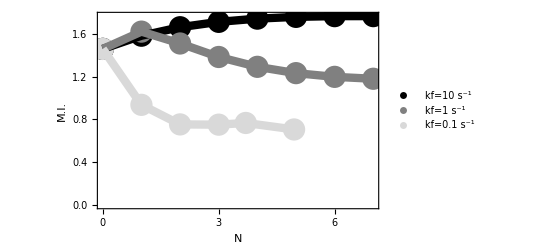

```mathematica
MIkf1={1.4586234168542846,1.6201963259109666,1.509360426851682,1.3831463627072238,1.291142465738909,1.2321310106120862,1.197423060641263,1.1795770826689};
MIkf10={1.458623416854282,1.5820537157474002,1.661444709778209,1.711523290947282,1.7416816409602305,1.7580998315221796,1.764945337975520,1.7651000926};

MIkf01={1.4586234168542838,0.9358591486210588,0.7528604190317278,0.7504920122990175,0.7663777316778799,0.7055385551710409};
(*{1.4586,0.93586,0.75286,0.75049,0.8038,0.8746,0.9491,1.020,1.0758,1.0948,1.200}; default integration method*)
MIkf1μ1σ2={2.1010413170152393,1.939991649078964,1.7801920904050719,1.7413582617142778,1.7173647306907396,1.7146611882781342,1.7237600820756558,1.7396216436820804};
MIkf10μ1σ2={2.101041317015243,2.136944802366786,2.1390110962123603,2.137734840665605,2.1044832915135023,2.09617625708177,2.088611079849956,2.1351653048528654};
MIkf01μ1σ2={{0,2.1010413157474845},{1,1.3320161093891159},{2,1.1920175744839234},{3,1.2247099091025684}};


comb1=Table[{j-1,MIkf1[[j]]},{j,1,Length[MIkf1]}];
comb2=Table[{j-1,MIkf10[[j]]},{j,1,Length[MIkf10]}];
comb3=Table[{j-1,MIkf01[[j]]},{j,1,Length[MIkf01]}];
comb3[[6,1]]=4.95;
comb3[[5,1]]=3.7;
comb4=Table[{j-1,MIkf1μ1σ2[[j]]},{j,1,Length[MIkf1μ1σ2]}];
comb5=Table[{j-1,MIkf10μ1σ2[[j]]},{j,1,Length[MIkf10μ1σ2]-1}];
comb6=MIkf01μ1σ2;

Fig2D=Legended[
Show[
ListPlot[{comb2,comb1,comb3},
Frame->{{True,False},{True,False}},FrameLabel->{"N","M.I."},LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{{PointSize[0.04],Black},{PointSize[0.04],Gray},{PointSize[0.04],LightGray}},FrameTicks->{{Automatic,None},{{0,1,2,3,4,5,6,7,8,9,10},None}},PlotRange->Automatic],
ListPlot[{comb2,comb1,comb3},Joined->True,PlotStyle->{{Black,Thickness[0.015]},{Gray,Thickness[0.015]},{LightGray,Thickness[0.015]}}]
],
PointLegend[{Black,Gray,LightGray},{"kf=10 s^-1","kf=1 s^-1","kf=0.1 s^-1"},LegendMarkerSize->25]
]
```

N::preclg: Requested precision 16 is larger than $MaxPrecision. Using current $MaxPrecision of 15.9546 instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

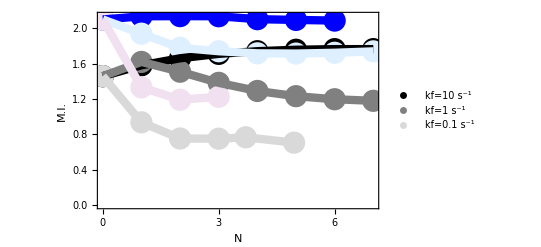

```mathematica
Legended[
Show[
ListPlot[{comb2,comb1,comb3,comb5,comb4,comb6},
Frame->{{True,False},{True,False}},FrameLabel->{"N","M.I."},LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{{PointSize[0.04],Black},{PointSize[0.04],Gray},{PointSize[0.04],LightGray},{PointSize[0.04],Blue},{PointSize[0.04],LightBlue},{PointSize[0.04],LightPurple}},FrameTicks->{{Automatic,None},{{0,1,2,3,4,5,6,7,8,9,10},None}},PlotRange->Automatic],
ListPlot[{comb2,comb1,comb3,comb5,comb4,comb6},Joined->True,PlotStyle->{{Black,Thickness[0.015]},{Gray,Thickness[0.015]},{LightGray,Thickness[0.015]},{Blue,Thickness[0.015]},{LightBlue,Thickness[0.015]},{LightPurple,Thickness[0.015]}}]
],
PointLegend[{Black,Gray,LightGray},{"kf=10 s^-1","kf=1 s^-1","kf=0.1 s^-1"},LegendMarkerSize->25]
]
```

```mathematica
MIfunc[i_]:=Module[{},
HNK=-NIntegrate[Pkoff[k]Pnlk[n,k,i] Log2[Pnlk[n,k,i]],{k,0.001,Infinity},{n,0.0,Infinity},Method->"MultiPeriodic"];
Pn[n_]:=NIntegrate[Pnlk[n,k,i]Pkoff[k],{k,0.001,Infinity},Method->"MultiPeriodic"];
HN=-NIntegrate[Pn[n]Log2[Pn[n]],{n,0.0,Infinity},Method->"Trapezoidal"];
HN-HNK];
MIfunc[6]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 155092 integrand evaluations. NIntegrate obtained 2.45071 and 0.00168034 for the integral and error estimates.

NIntegrate::inumr: The integrand (ⅇ^(-1/2 Log[-0.999+Power[«2»]]^2-(n-«1»)^2/(2 («1»))) (1-Cos[2 k π]))/(2 π «1» («1») √(200/((-0.999+1/Plus[«3»]) (0.001+1/Plus[«3»]) (1+10. Plus[«2»])^6)+100/((«1») «1»«1»«1»)-(200 (2+1/(«1»)+10. (-0.999+Power[«2»]) (8+Times[«2»])))/((-0.999+1/(«1»))^3 (1+«1»)^3 (1+10. «1»)^13))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{Indeterminate,Indeterminate}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.949096

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["Fig2D.pdf",Fig2D];
```

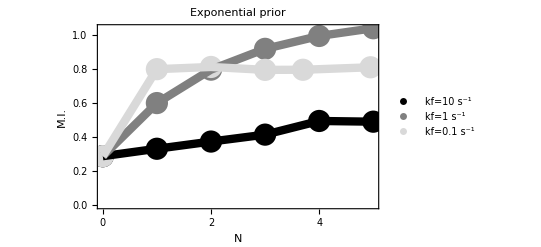

```mathematica
MIkf1ExpPriorK={0.2885,0.60130,0.79820,0.920567,0.996506,1.04198};
MIkf10ExpPriorK={0.2885,0.33225,0.374648,0.41543,0.4958737,0.4916966};
MIkf01ExpPriorK={0.28849,0.800944,0.81392,0.79680,0.797432,0.8120359};

comb1Exp=Table[{j-1,MIkf1ExpPriorK[[j]]},{j,1,Length[MIkf1ExpPriorK]}];
comb2Exp=Table[{j-1,MIkf10ExpPriorK[[j]]},{j,1,Length[MIkf10ExpPriorK]}];
comb3Exp=Table[{j-1,MIkf01ExpPriorK[[j]]},{j,1,Length[MIkf01ExpPriorK]}];
comb3Exp[[6,1]]=4.95;
comb3Exp[[5,1]]=3.7;

Legended[
Show[
ListPlot[{comb2Exp,comb1Exp,comb3Exp},
Frame->{{True,False},{True,False}},FrameLabel->{"N","M.I."},LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{{PointSize[0.04],Black},{PointSize[0.04],Gray},{PointSize[0.04],LightGray}},FrameTicks->{{Automatic,None},{{0,1,2,3,4,5},None}},PlotRange->Automatic,PlotLabel->"Exponential prior"],
ListPlot[{comb2Exp,comb1Exp,comb3Exp},Joined->True,PlotStyle->{{Black,Thickness[0.015]},{Gray,Thickness[0.015]},{LightGray,Thickness[0.015]}}]
],
PointLegend[{Black,Gray,LightGray},{"kf=10 s^-1","kf=1 s^-1","kf=0.1 s^-1"},LegendMarkerSize->25]
]
```

Can also use the formulation of the mutual information as lower bounded by the Fisher Information:
I[k_off,n]≥ H[k_off]-∫dk_off P(k_off)1/2 ln[(2πe)/(J(k_off))]

```mathematica
DlnPnlkDk=(kp t x (1+x)^4 ((1+g)^(1+Ns) koff π (1+x)^2 (1+g (1+Ns+Ns x))+kp (2 (1+g)^Ns+(-6+5 (1+g)^Ns) x+4 (-1+(1+g)^Ns) x^2+(-1+(1+g)^Ns) x^3+g^2 (2 (1+g)^Ns+(-6+5 (1+g)^Ns) x+4 (-1+(1+g)^Ns) x^2+(-1+(1+g)^Ns) x^3-2 Ns^2 x (1+x)^2+Ns (1+x) ((1+g)^Ns+(-7+2 (1+g)^Ns) x+(-3+(1+g)^Ns) x^2))+g (Ns (1+x) ((1+g)^Ns+2 (-3+(1+g)^Ns) x+(-2+(1+g)^Ns) x^2)+2 (2 (1+g)^Ns+(-6+5 (1+g)^Ns) x+4 (-1+(1+g)^Ns) x^2+(-1+(1+g)^Ns) x^3))))+((1+g)^(-1+Ns) (n-((1+g)^-Ns kp t x)/(1+x)) ((1+g)^(1+Ns) koff π (1+x)^2+kp ((1+g)^Ns+2 (-1+(1+g)^Ns) x+(-1+(1+g)^Ns) x^2+g ((1+g)^Ns+(-2+2 (1+g)^Ns-Ns) x+(-1+(1+g)^Ns-Ns) x^2))) (-2 kp t x (1+g (1+Ns+Ns x)) ((1+g)^(1+Ns) koff (1+x)^2+2 kp ((1+g)^Ns+2 (-1+(1+g)^Ns) x+(-1+(1+g)^Ns) x^2+g ((1+g)^Ns+(-2+2 (1+g)^Ns-Ns) x+(-1+(1+g)^Ns-Ns) x^2)))+(kp t x-(1+g)^Ns n (1+x)) ((1+g)^(1+Ns) koff (1+x)^2 (1+g (1+Ns+Ns x))+2 kp (2 (1+g)^Ns+(-6+5 (1+g)^Ns) x+4 (-1+(1+g)^Ns) x^2+(-1+(1+g)^Ns) x^3+g^2 (2 (1+g)^Ns+(-6+5 (1+g)^Ns) x+4 (-1+(1+g)^Ns) x^2+(-1+(1+g)^Ns) x^3-2 Ns^2 x (1+x)^2+Ns (1+x) ((1+g)^Ns+(-7+2 (1+g)^Ns) x+(-3+(1+g)^Ns) x^2))+g (Ns (1+x) ((1+g)^Ns+2 (-3+(1+g)^Ns) x+(-2+(1+g)^Ns) x^2)+2 (2 (1+g)^Ns+(-6+5 (1+g)^Ns) x+4 (-1+(1+g)^Ns) x^2+(-1+(1+g)^Ns) x^3))))))/(koff ((1+g)^Ns/(1+x)+(2 (1+g)^Ns kp)/(koff+koff x)-(2 kp x (2+x+g (2+Ns+x+Ns x)))/((1+g) koff (1+x)^3))^2))/(2 (1+g)^2 koff^2 kp t x (1+x)^8 (((1+g)^Ns π)/(1+x)+((1+g)^Ns kp)/(koff+koff x)-(kp x (2+x+g (2+Ns+x+Ns x)))/((1+g) koff (1+x)^3)))/.expandParams;
```

```mathematica
Pkoff[koff_]:=1/(koff √(2π))E^(-1/2 Log[koff]^2);(*Log-normal PDF*)
Pnlk[n_,koff_,Ns_]:=Module[{c=1,kf=1,kon=1,kp=1,t=100,σn,μ},
μ=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff));
σn=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff))+(2 c (1+koff/kf)^-Ns kon kp^2 t)/(koff (koff+c kon))-(2 c^2 (1+koff/kf)^(-1-2 Ns) kon^2 kp^2 (2+(c kon)/koff+(koff (2+(c kon)/koff+Ns+(c kon Ns)/koff))/kf) t)/(koff^3 (1+(c kon)/koff)^3);
1/(√(2π σn))E^(-1/2((n-μ)/(√σn))^2)];
FI[koff_,Ns_,KF_]:=Module[{c=1,kf=KF,kon=1,kp=1,t=100},
NIntegrate[(((1/koff c kon (1+(c kon)/koff)^4 kp (kp (2 (1+koff/kf)^Ns+(c (-6+5 (1+koff/kf)^Ns) kon)/koff+(4 c^2 (-1+(1+koff/kf)^Ns) kon^2)/koff^2+(c^3 (-1+(1+koff/kf)^Ns) kon^3)/koff^3+1/kf koff (2 (2 (1+koff/kf)^Ns+(c (-6+5 (1+koff/kf)^Ns) kon)/koff+(4 c^2 (-1+(1+koff/kf)^Ns) kon^2)/koff^2+(c^3 (-1+(1+koff/kf)^Ns) kon^3)/koff^3)+(1+(c kon)/koff) ((1+koff/kf)^Ns+(2 c (-3+(1+koff/kf)^Ns) kon)/koff+(c^2 (-2+(1+koff/kf)^Ns) kon^2)/koff^2) Ns)+1/kf^2 koff^2 (2 (1+koff/kf)^Ns+(c (-6+5 (1+koff/kf)^Ns) kon)/koff+(4 c^2 (-1+(1+koff/kf)^Ns) kon^2)/koff^2+(c^3 (-1+(1+koff/kf)^Ns) kon^3)/koff^3+(1+(c kon)/koff) ((1+koff/kf)^Ns+(c (-7+2 (1+koff/kf)^Ns) kon)/koff+(c^2 (-3+(1+koff/kf)^Ns) kon^2)/koff^2) Ns-(2 c kon (1+(c kon)/koff)^2 Ns^2)/koff))+koff (1+koff/kf)^(1+Ns) (1+(c kon)/koff)^2 (1+(koff (1+Ns+(c kon Ns)/koff))/kf) π) t+((1+koff/kf)^(-1+Ns) (kp ((1+koff/kf)^Ns+(2 c (-1+(1+koff/kf)^Ns) kon)/koff+(c^2 (-1+(1+koff/kf)^Ns) kon^2)/koff^2+(koff ((1+koff/kf)^Ns+(c^2 kon^2 (-1+(1+koff/kf)^Ns-Ns))/koff^2+(c kon (-2+2 (1+koff/kf)^Ns-Ns))/koff))/kf)+koff (1+koff/kf)^(1+Ns) (1+(c kon)/koff)^2 π) (n-(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff))) (-1/koff 2 c kon kp (koff (1+koff/kf)^(1+Ns) (1+(c kon)/koff)^2+2 kp ((1+koff/kf)^Ns+(2 c (-1+(1+koff/kf)^Ns) kon)/koff+(c^2 (-1+(1+koff/kf)^Ns) kon^2)/koff^2+(koff ((1+koff/kf)^Ns+(c^2 kon^2 (-1+(1+koff/kf)^Ns-Ns))/koff^2+(c kon (-2+2 (1+koff/kf)^Ns-Ns))/koff))/kf)) (1+(koff (1+Ns+(c kon Ns)/koff))/kf) t+(koff (1+koff/kf)^(1+Ns) (1+(c kon)/koff)^2 (1+(koff (1+Ns+(c kon Ns)/koff))/kf)+2 kp (2 (1+koff/kf)^Ns+(c (-6+5 (1+koff/kf)^Ns) kon)/koff+(4 c^2 (-1+(1+koff/kf)^Ns) kon^2)/koff^2+(c^3 (-1+(1+koff/kf)^Ns) kon^3)/koff^3+1/kf koff (2 (2 (1+koff/kf)^Ns+(c (-6+5 (1+koff/kf)^Ns) kon)/koff+(4 c^2 (-1+(1+koff/kf)^Ns) kon^2)/koff^2+(c^3 (-1+(1+koff/kf)^Ns) kon^3)/koff^3)+(1+(c kon)/koff) ((1+koff/kf)^Ns+(2 c (-3+(1+koff/kf)^Ns) kon)/koff+(c^2 (-2+(1+koff/kf)^Ns) kon^2)/koff^2) Ns)+1/kf^2 koff^2 (2 (1+koff/kf)^Ns+(c (-6+5 (1+koff/kf)^Ns) kon)/koff+(4 c^2 (-1+(1+koff/kf)^Ns) kon^2)/koff^2+(c^3 (-1+(1+koff/kf)^Ns) kon^3)/koff^3+(1+(c kon)/koff) ((1+koff/kf)^Ns+(c (-7+2 (1+koff/kf)^Ns) kon)/koff+(c^2 (-3+(1+koff/kf)^Ns) kon^2)/koff^2) Ns-(2 c kon (1+(c kon)/koff)^2 Ns^2)/koff))) (-(1+koff/kf)^Ns (1+(c kon)/koff) n+(c kon kp t)/koff)))/(koff ((1+koff/kf)^Ns/(1+(c kon)/koff)+(2 (1+koff/kf)^Ns kp)/(koff+c kon)-(2 c kon kp (2+(c kon)/koff+(koff (2+(c kon)/koff+Ns+(c kon Ns)/koff))/kf))/(koff^2 (1+koff/kf) (1+(c kon)/koff)^3))^2))/(2 c koff (1+koff/kf)^2 kon (1+(c kon)/koff)^8 kp (((1+koff/kf)^Ns kp)/(koff+c kon)-(c kon kp (2+(c kon)/koff+(koff (2+(c kon)/koff+Ns+(c kon Ns)/koff))/kf))/(koff^2 (1+koff/kf) (1+(c kon)/koff)^3)+((1+koff/kf)^Ns π)/(1+(c kon)/koff)) t)))^2(ⅇ^(-((-(100 (1+koff)^-Ns)/((1+1/koff) koff)+n)^2)/(2 ((200 (1+koff)^(-1-Ns))/koff+(100 (1+koff)^-Ns)/((1+1/koff) koff)-(200 (1+koff)^(-1-2 Ns) (2+1/koff+koff (2+1/koff+Ns+Ns/koff)))/((1+1/koff)^3 koff^3)))))/(√((200 (1+koff)^(-1-Ns))/koff+(100 (1+koff)^-Ns)/((1+1/koff) koff)-(200 (1+koff)^(-1-2 Ns) (2+1/koff+koff (2+1/koff+Ns+Ns/koff)))/((1+1/koff)^3 koff^3)) √(2 π)),{n,0,Infinity}]
]

MIviaFI[Ns_,KF_]:=Module[{HNK,HK},
HNK=NIntegrate[Pkoff[k] 1/2 Log[2π E/FI[k,Ns,KF]],{k,10^-6,Infinity}];
HK=-NIntegrate[Pkoff[k]Log2[Pkoff[k]],{k,0,Infinity}];
HK-HNK
]
```

```mathematica
FI[0.1,4,1]
```

438.588

```mathematica
MIviaFIList=Table[{i,MIviaFI[i,1]},{i,0,5}]
```

{{0,1.55958},{1,1.75482},{2,1.75789},{3,1.73713},{4,2.0471-NIntegrate[1/2 Pkoff[k] Log[(2 π ⅇ)/FI[k,4,1]],{k,1/10^6,∞}]},{5,2.0471-NIntegrate[1/2 Pkoff[k] Log[(2 π ⅇ)/FI[k,5,1]],{k,1/10^6,∞}]}}

#### Derivations for G-protein KPR mean and variance

```mathematica
M0={{-kon c,koff},{kon c , -koff}};
M1={{-kon c,koff,koff},{kon c,-koff-kf,0},{0,kf,-koff}};
M2={{-kon c,koff,koff,koff},{kon c,-koff-kf,0,0},{0,kf,-koff-kf,0},{0,0,kf,-koff}};
M3={{-kon c,koff,koff,koff,koff},{kon c,-koff-kf,0,0,0},{0,kf,-koff-kf,0,0},{0,0,kf,-koff-kf,0},{0,0,0,kf,-koff}};
M4={{-kon c,koff,koff,koff,koff,koff},{kon c,-koff-kf,0,0,0,0},{0,kf,-koff-kf,0,0,0},{0,0,kf,-koff-kf,0,0},{0,0,0,kf,-koff-kf,0},{0,0,0,0,kf,-koff}};
M5={{-kon c,koff,koff,koff,koff,koff,koff},{kon c,-koff-kf,0,0,0,0,0},{0,kf,-koff-kf,0,0,0,0},{0,0,kf,-koff-kf,0,0,0},{0,0,0,kf,-koff-kf,0,0},{0,0,0,0,kf,-koff-kf,0},{0,0,0,0,0,kf,-koff}};
```

```mathematica
Pss0={P0,P1}/.(Solve[Join[Table[(M0.{P0,P1})[[i]]==0,{i,1,1}],{P0+P1==1}],{P0,P1}][[1]]);
Pss1={P0,P1,P2}/.(Solve[Join[Table[(M1.{P0,P1,P2})[[i]]==0,{i,1,2}],{P0+P1+P2==1}],{P0,P1,P2}][[1]]);
Pss2={P0,P1,P2,P3}/.(Solve[Join[Table[(M2.{P0,P1,P2,P3})[[i]]==0,{i,1,3}],{P0+P1+P2+P3==1}],{P0,P1,P2,P3}][[1]]);
Pss3={P0,P1,P2,P3,P4}/.(Solve[Join[Table[(M3.{P0,P1,P2,P3,P4})[[i]]==0,{i,1,4}],{P0+P1+P2+P3+P4==1}],{P0,P1,P2,P3,P4}][[1]]);
Pss4={P0,P1,P2,P3,P4,P5}/.(Solve[Join[Table[(M4.{P0,P1,P2,P3,P4,P5})[[i]]==0,{i,1,5}],{P0+P1+P2+P3+P4+P5==1}],{P0,P1,P2,P3,P4,P5}][[1]]);
Pss5={P0,P1,P2,P3,P4,P5,P6}/.(Solve[Join[Table[(M5.{P0,P1,P2,P3,P4,P5,P6})[[i]]==0,{i,1,6}],{P0+P1+P2+P3+P4+P5+P6==1}],{P0,P1,P2,P3,P4,P5,P6}][[1]]);
```

```mathematica
mMean[M_,Pss_]:=Module[{ndims=Length[Pss]},M[[ndims,ndims-1]] t Pss[[ndims-1]]]

mVariance[M_,Pss_]:=Module[{ndims,npartials,nEqs,nfVec,nSol,nSubMeans,dNSQUAREdt,NSQUARE,meanM,CovNN},
ndims=Length[M];
npartials=Table[Symbol["n"<>ToString[i]],{i,1,ndims}];
nfVec=Table[0,{i,1,ndims}];
nfVec[[ndims]]=M[[ndims,ndims-1]] Pss[[ndims-1]];

nEqs=Join[
Table[D[npartials[[i]][t],t]==M[[i]].Table[npartials[[i]][t],{i,1,ndims}]+nfVec[[i]],{i,1,ndims}],
Table[npartials[[i]][0]==0,{i,1,ndims}]];
nSol=DSolve[nEqs,npartials,t];
nSubMeans=Table[Evaluate[npartials/.nSol[[1]]][[i,2]],{i,1,ndims}];

dNSQUAREdt=2M[[ndims,ndims-1]] nSubMeans[[ndims-1]]+M[[ndims,ndims-1]] Pss[[ndims-1]];
NSQUARE=Integrate[dNSQUAREdt,t] // Simplify ;
meanM=M[[ndims,ndims-1]] t Pss[[ndims-1]];
CovNN=NSQUARE- meanM^2//Simplify;
CovNN
]
contractParams={c->(koff x)/kon,kf->koff/g};
expandParams={x->(kon c)/koff,g->koff/kf};
noExp={ⅇ^(-koff t (1+x))->0,ⅇ^(-(koff t (1+g+g x))/g)->0,ⅇ^(-(koff t (1+g (2+x)))/g)->0,ⅇ^(-((1+g) koff t)/g)->0,ⅇ^(-t (2 koff+koff/g+koff x))->0};
```

```mathematica
(* Confirmed from PRE paper *)
mMean[M0,Pss0]/.contractParams//Simplify
(mVariance[M0,Pss0]/.contractParams//FullSimplify)/.noExp
```

(koff t x)/(1+x)

(koff t x (1+x^2))/(1+x)^3

```mathematica
mMean[M1,Pss1]/.contractParams//Simplify
(mVariance[M1,Pss1]/.contractParams//FullSimplify)/.noExp
```

(koff t x)/(1+g+x+g x)

(koff t x (1+2 g+x^2+g^2 (1+x)^2))/((1+g)^3 (1+x)^3)

```mathematica
mMean[M2,Pss2]/.contractParams//Simplify
(mVariance[M2,Pss2]/.contractParams//FullSimplify)/.noExp//FullSimplify
```

(koff t x)/((1+g)^2 (1+x))

(koff t x ((1+g)^3+2 g^2 (3+g) x+(1+g (-1+g (3+g))) x^2))/((1+g)^5 (1+x)^3)

```mathematica
mMean[M3,Pss3]/.contractParams//Simplify
(mVariance[M3,Pss3]/.contractParams//FullSimplify)/.noExp//FullSimplify
```

(koff t x)/((1+g)^3 (1+x))

(koff t x ((1+g)^4+2 g^2 (6+g (4+g)) x+(1+g (-2+g (6+g (4+g)))) x^2))/((1+g)^7 (1+x)^3)

```mathematica
mMean[M4,Pss4]/.contractParams//Simplify
(mVariance[M4,Pss4]/.contractParams)/.noExp//Simplify
```

(koff t x)/((1+g)^4 (1+x))

(koff t x (1+x^2+10 g^2 (1+x)^2+10 g^3 (1+x)^2+5 g^4 (1+x)^2+g^5 (1+x)^2+g (5-3 x^2)))/((1+g)^9 (1+x)^3)

```mathematica
mMean[M5,Pss5]/.contractParams//Simplify
(mVariance[M5,Pss5]/.contractParams)/.noExp//Simplify
```

(koff t x)/((1+g)^5 (1+x))

-(koff^2 t^2 x^2)/((1+g)^10 (1+x)^2)

#### Plotting G-protein KPR & Burst Model Simulations

```mathematica
MeanM0=β(koff t x)/(1+x);
VarM0=β^2(koff t x (1+x^2))/(1+x)^3;(*(x (-2 ⅇ^(-koff t (1+x)) x+koff t (1+x) (1+x^2)))/(1+x)^4;*)
MeanM1=β(koff t x)/((1+x)(1+g));
VarM1=β^2(koff t x (1+2 g+x^2+g^2 (1+x)^2))/((1+g)^3 (1+x)^3);
MeanM2=β(koff t x)/((1+g)^2 (1+x));
VarM2=β^2(koff t x ((1+g)^3+2 g^2 (3+g) x+(1+g (-1+g (3+g))) x^2))/((1+g)^5 (1+x)^3);
MeanM3=β(koff t x)/((1+g)^3 (1+x));
VarM3=β^2(koff t x ((1+g)^4+2 g^2 (6+g (4+g)) x+(1+g (-2+g (6+g (4+g)))) x^2))/((1+g)^7 (1+x)^3);
MeanM4=β(koff t x)/((1+g)^4 (1+x));
VarM4=β^2(koff t x (1+x^2+10 g^2 (1+x)^2+10 g^3 (1+x)^2+5 g^4 (1+x)^2+g^5 (1+x)^2+g (5-3 x^2)))/((1+g)^9 (1+x)^3);
MeanM5=(koff t x)/((1+g)^5 (1+x));


Σk0G=(VarM0/.expandParams)/D[Evaluate[MeanM0/.expandParams],koff]^2//Simplify;
Σk1G=(VarM1/.expandParams)/D[Evaluate[MeanM1/.expandParams],koff]^2//Simplify;
Σk2G=(VarM2/.expandParams)/D[Evaluate[MeanM2/.expandParams],koff]^2//Simplify;
Σk3G=(VarM3/.expandParams)/D[Evaluate[MeanM3/.expandParams],koff]^2//Simplify;
Σk4G=(VarM4/.expandParams)/D[Evaluate[MeanM4/.expandParams],koff]^2//Simplify;


KPRG0FLD=BPMetric[koff,Σk0G];
KPRG1FLD=BPMetric[koff,Σk1G];
KPRG2FLD=BPMetric[koff,Σk2G];
KPRG3FLD=BPMetric[koff,Σk3G];
KPRG4FLD=BPMetric[koff,Σk4G];

KPRG0HN=(MeanM0/.expandParams/.koff->δ koff)/(MeanM0/.expandParams);
KPRG1HN=(MeanM1/.expandParams/.koff->δ koff)/(MeanM1/.expandParams);
KPRG2HN=(MeanM2/.expandParams/.koff->δ koff)/(MeanM2/.expandParams);
KPRG3HN=(MeanM3/.expandParams/.koff->δ koff)/(MeanM3/.expandParams);
KPRG4HN=(MeanM4/.expandParams/.koff->δ koff)/(MeanM4/.expandParams);
KPRGNHN=(((koff t x)/((1+g)^Ns (1+x)))/.expandParams/.koff->δ koff)/(((koff t x)/((1+g)^Ns (1+x)))/.expandParams);
```

Note that the variance in the G-protein signal has an asymptote for each model N with N>0. Avoid choosing conditions that match the asymptote for both koff and δ×koff.

```mathematica
xgParams
```

{kon→1,kp→1,t→100,koff→10^gtest,δ→0.1,c→10^ctest,kf→1}

```mathematica
testpoint={ctest->1,gtest->0,β->1};
testpoint2={ctest->1,gtest->Log10[3],β->1};


AnyTrue[Table[Abs[ΣkGundefined/.Ns->i/.xgParams/.testpoint],{i,1,4}],#<0.01&]
AnyTrue[Table[Abs[ΣkGundefined/.Ns->i/.xgParams/.testpoint2],{i,1,4}],#<0.01&]
AnyTrue[Table[Abs[ΣkGundefined/.{Ns->i,koff->δ koff}/.xgParams/.testpoint],{i,1,4}],#<0.01&]
AnyTrue[Table[Abs[ΣkGundefined/.{Ns->i,koff->δ koff}/.xgParams/.testpoint2],{i,1,4}],#<0.01&]
```

False

False

False

«1 more identical outputs»

```mathematica
Table[ΣkGundefined/.{koff->10,kf->1,c->1,kon->1,δ->0.1},{Ns,0,6}]
Table[ΣkGundefined/.{koff->5,kf->1,c->1,kon->1,δ->0.1},{Ns,0,6}]
```

{-11,99,209,319,429,539,649}

{-6,24,54,84,114,144,174}

```mathematica
KPRG0FLD/.contractParams//Simplify
KPRG1FLD/.contractParams//Simplify
KPRG2FLD/.contractParams//Simplify
```

(koff t x^3 (-1+δ)^2)/(1+δ^4+x^3 (1+δ)+x^2 (1+δ^2)+x (1+δ^3))

(t x (koff-koff δ)^2)/(koff (((1+g) (1+x) (1+2 g+x^2+g^2 (1+x)^2))/(g-x)^2+(δ (x+δ) (1+g δ) (2 g^2 x δ^3+δ^2 (1+g δ)^2+x^2 (1+g^2 δ^2)))/((x-g δ^2)^2)))

(t x (koff-koff δ)^2)/(koff (((1+g) (1+x) (1+x^2+3 g^2 (1+x)^2+g^3 (1+x)^2-g (-3+x^2)))/(x-g (2+x))^2+(δ (x+δ) (1+g δ) (δ^2 (1+g δ)^3+2 g^2 x δ^3 (3+g δ)+x^2 (1-g δ+3 g^2 δ^2+g^3 δ^3)))/((2 g δ^2+x (-1+g δ))^2)))

```mathematica
Limit[Out[184],x->Infinity]
Limit[Out[185],x->Infinity]

Limit[Out[186],x->Infinity]
```

%184

%185

%186

```mathematica
1+δ/.δ->0.1
1+δ+g (1+δ^2)+g^2 (1+δ^3)+g^3 (1+δ^4)/.{δ->0.1,g->10}
1+δ-4 g δ+4 g^3 (-1+δ)^2 (1+δ+δ^2)+g^2 (2+δ+δ^2+2 δ^3)-2 g^5 δ (1-2 δ-2 δ^3+δ^4)+g^6 (δ^2+δ^5)+g^4 (1-8 δ+2 δ^2+2 δ^3-8 δ^4+δ^5)/.{δ->0.1,g->10}
```

1.1

1111.4

64.8

```mathematica
MeanM1/.{x->0.5,koff->10,g->10,t->100,β->1}//N
MeanM1/.{x->5,koff->1,g->1,t->100,β->1}//N

Solve[Evaluate[MeanM1/.expandParams/.koff->δ koff]==Evaluate[MeanM1/.expandParams],c]
```

```mathematica
((MeanM1/.expandParams/.koff->ζ koff)-(MeanM1/.expandParams))/((MeanM0/.expandParams/.koff->ζ koff)-(MeanM0/.expandParams))//Simplify

(MeanM1/.expandParams/.koff->ζ koff)-(MeanM1/.expandParams)//Simplify
```

(kf (c kf kon-koff^2 ζ))/(c (kf+koff) kon (kf+koff ζ))

(c kf koff kon t β (-1+ζ) (c kf kon-koff^2 ζ))/((kf+koff) (koff+c kon) (kf+koff ζ) (c kon+koff ζ))

```mathematica
10^2 0.1/1
```

10.

```mathematica
MeanM1/.expandParams
```

(c kon t β)/((1+koff/kf) (1+(c kon)/koff))

```mathematica
MeanM1
```

(koff t x β)/((1+g) (1+x))

```mathematica
MeanM1-(MeanM1/.{koff->ζ koff,x->x/ζ,g->ζ g})//Simplify
```

(koff t x β (-1+ζ) (-x+g ζ))/((1+g) (1+x) (x+ζ) (1+g ζ))

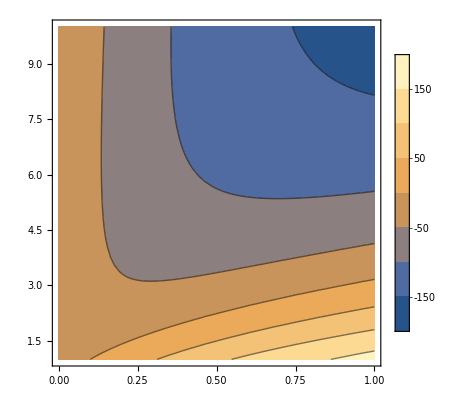

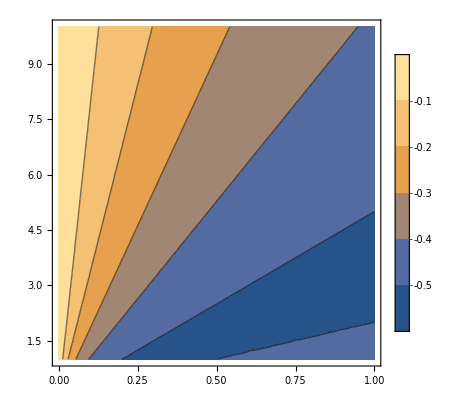

```mathematica
ContourPlot[((c kon t β)/((1+koff/kf) (1+(c kon)/koff))-(c kon t β)/((1+(ζ koff)/kf) (1+(c kon)/(ζ koff))))/.{kon->1,kf->1,β->10,t->100,ζ ->0.1},{c,0,1},{koff,1,10},PlotLegends->Automatic]
ContourPlot[( (kon c/koff)/(kon c/koff+1)-(kon c/(ζ koff))/(kon c/(ζ koff)+1))/.{kon->1,kf->1,β->10,t->100,ζ ->0.1},{c,0,1},{koff,1,10},PlotLegends->Automatic]
```

```mathematica
HNReviwer2ModelSimMedC={{0,1.00},{1,3.30},{2,17.04},{3,87.55},{4,796.22}};

FLDReviewer2ModelSimHighC={{0,1.00},{1,82.52},{2,326.91},{3,204.24},{4,94.01}};
FLDReviewer2ModelSimMedC={{0,1.00},{1,706.11},{2,798.36},{3,371.34},{4,149.72}};
FLDReviewer2ModelSimLowC={{0,1.00},{1,733.09},{2,523.14},{3,318.13},{4,135.05}};

FLDReviewer2ModelSimτIs1OverKOFF={{0,1.0000},{1,2.1582},{2,4.4224},{3,4.1726},{4,3.9602},{5,2.7774}};(*{{0,1.0000},{1,0.6348},{2,1.7117},{3,1.9624},{4,1.6613},{5,1.2238}};*)
FLDReviewer2ModelSimτIs1OverKOFHighG={{0,1.0000},{1,2.6509},{2,2.2813},{3,1.3466},{4,0.6453},{5,0.2547}};(*{{0,1.00},{1,0.7261},{2,0.86},{3,0.35},{4,0.17},{5,0.0865}};*)
(*FLDReviewer2ModelSimτIs1OverKOFG100={{0,1.0000},{1,0.1347},{2,0.0200},{3,0.0019},{4,0.0001}};*)

FLDReviewer2ModelSimτIs1OverKOFFLowC={{0,1.0000},{1,1073.7280},{2,758.3255},{3,316.6415},{4,269.3606},{5,107.7563}};(*{{0,1.0000},{1,71.1346},{2,56.0861},{3,31.7410},{4,16.0192}};*)
FLDReviewer2ModelSimτIs1OverKOFFHighC={{0,1.0000},{1,0.0071},{2,0.0606},{3,0.0340},{4,0.0137},{5,0.0065}};(*{{0,1.0000},{1,0.0004},{2,0.0081},{3,0.0065},{4,0.0028}};*)

AllDetFLD={{0,1.0000},{1,1.5281},{2,4.3959},{3,4.9465},{4,3.7004}};(*{{0,1.0000},{1,0.2919},{2,1.2353},{3,1.3128},{4,1.0823}};*)
AllDetFLDHighG={{0,1.0000},{1,2.4888},{2,1.5772},{3,1.0520},{4,0.4475}};(*{{0,1.0000},{1,0.5656},{2,0.5865},{3,0.2972},{4,0.1290}};*)
AllDetHN={{0,1.00},{1,3.03},{2,8.51},{3,24.21},{4,94.45}};(*{{0,1.0000},{1,(450.406-451.4904)^2/(3916.3512+1146.4187)},{2,0.0180},{3,0.0126},{4,0.0055}};*)
```

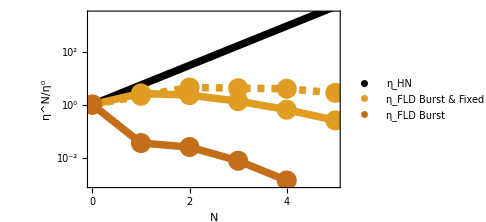
-Graphics--Graphics-

```mathematica
SNRn=μN/ΣN/.contractParams;
SNR0=μ0/Σ0/.contractParams;

testpoint={ctest->1,gtest->1,β->10};
testpoint2={ctest->1,gtest->1,kf->10/3,β->10};
yticks=Table[{2.301i,Superscript[10,i]},{i,-4,4}];
p1=ListLogPlot[Table[{Ns,ηN/η0}/.xgParams/.testpoint,{Ns,0,5,1}],Frame->{{True,False},{True,False}},FrameLabel->{"N","η^N/η^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{PointSize[0.00],Black},FrameTicks->{{yticks,None},{{0,1,2,3,4,5},None}},PlotRange->{Automatic,{0.001,2500}}];
p2=LogPlot[KPRGNHN/KPRG0HN/.xgParams/.testpoint,{Ns,0,5},PlotStyle->{Thickness[0.015],Black}];


BPKscale={{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk}}/.xgParams/.testpoint;
BPKscale2={{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk}}/.xgParams/.testpoint;
FLDReviewer2ModelSim={{0,1.00},{1,1044.30},{2,553.45},{3,215.77},{4,92.01}};
FLDReviewer2ModelSimHighG={{0,1.00},{1,652.46},{2,84.63},{3,6.89},{4,0.64}};
(*{{0,1.00},{1,1823.27},{2,251.27},{3,25.63},{4,2.32}}*)
KPRGFLD1={{0,1},{1,KPRG1FLD/KPRG0FLD},{2,KPRG2FLD/KPRG0FLD},{3,KPRG3FLD/KPRG0FLD},{4,KPRG4FLD/KPRG0FLD}}/.xgParams/.testpoint;

g1=Legended[
Show[p1,p2,

(*ListLogPlot[BPKscale,PlotStyle->{cmap[[3]],PointSize[0.04]}],
ListLogPlot[BPKscale,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015]}],

ListLogPlot[BPKscale2,PlotStyle->{cmap[[3]],PointSize[0.04],Opacity[0.75]}],
ListLogPlot[BPKscale2,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015],Dashing[0.01],Opacity[0.5]}],*)


ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,PlotStyle->{cmap[[2]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,Joined->True,PlotStyle->{cmap[[2]],Thickness[0.015],Dashed}],

ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFHighG,PlotStyle->{cmap[[2]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFHighG,Joined->True,PlotStyle->{cmap[[2]],Thickness[0.015]}],

ListLogPlot[KPRGFLD1,PlotStyle->{cmap[[6]],PointSize[0.04]}],
ListLogPlot[KPRGFLD1,Joined->True,PlotStyle->{cmap[[6]],Thickness[0.015]}],

ImageSize->Medium
],
PointLegend[{Black,cmap[[2]],cmap[[6]]},{"η_HN","η_FLD\nBurst &\nFixed residence time","η_FLD\nBurst"},LegendMarkerSize->25]];
g2=LogPlot[SNRn/SNR0/.expandParams/.xgParams/.Ns->Ntest/.testpoint,{Ntest,0,4},
Frame->{{True,False},{True,False}},FrameLabel->{"N","SNR^N/SNR^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{Black,Thickness[0.015]},FrameTicks->{{Automatic,None},{{0,1,2,3,4},None}},ImageSize->Medium];
Fig4A=g1;
Fig3C=g2;
Row[{g1,g2}]
```

```mathematica
KPRG1FLD/KPRG0FLD/.{c->1,kon->1,koff->10,kf->10/3,kp->1,t->100,δ->0.1}
```

11.6718

```mathematica
(*g1=Legended[
Show[p1,p2,

(*ListLogPlot[BPKscale,PlotStyle->{cmap[[3]],PointSize[0.04]}],
ListLogPlot[BPKscale,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015]}],

ListLogPlot[BPKscale2,PlotStyle->{cmap[[3]],PointSize[0.04],Opacity[0.75]}],
ListLogPlot[BPKscale2,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015],Dashing[0.01],Opacity[0.5]}],*)


ListLogPlot[FLDReviewer2ModelSim,PlotStyle->{cmap[[2]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSim,Joined->True,PlotStyle->{cmap[[2]],Thickness[0.015]}],

ListLogPlot[FLDReviewer2ModelSimHighG,PlotStyle->{cmap[[2]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimHighG,Joined->True,PlotStyle->{cmap[[2]],Thickness[0.015],Dashed}],

ListLogPlot[KPRGFLD1,PlotStyle->{cmap[[6]],PointSize[0.04]}],
ListLogPlot[KPRGFLD1,Joined->True,PlotStyle->{cmap[[6]],Thickness[0.015]}],

ImageSize->Medium
],
PointLegend[{Black,cmap[[2]],cmap[[6]]},{"η_HN","η_FLD\nBurst &\nFixed residence time","η_FLD\nBurst"},LegendMarkerSize->25]];
g2=LogPlot[SNRn/SNR0/.expandParams/.xgParams/.Ns->Ntest/.testpoint,{Ntest,0,4},
Frame->{{True,False},{True,False}},FrameLabel->{"N","SNR^N/SNR^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{Black,Thickness[0.015]},FrameTicks->{{Automatic,None},{{0,1,2,3,4},None}},ImageSize->Medium];
Fig4A=g1;
Fig3C=g2;
Row[{g1,g2}]*)
```

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["Fig4A.pdf",Fig4A];
Export["Fig3C.pdf",Fig3C];
```

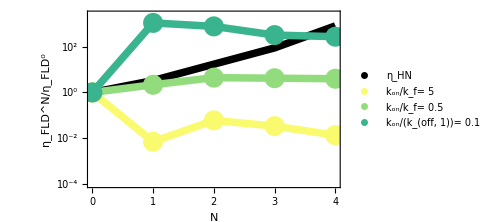

```mathematica
FigS1H=Legended[
Show[
ListLogPlot[HNReviwer2ModelSimMedC,Frame->{{True,False},{True,False}},FrameLabel->{"N","η_FLD^N/η_FLD^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{PointSize[0.00],Black},FrameTicks->{{yticks,None},{{0,1,2,3,4},None}},PlotRange->{Automatic,{0.0001,2500}}],
(*LogPlot[KPRGNHN/KPRG0HN/.xgParams/.testpoint,{Ns,0,4},PlotStyle->{Thickness[0.015],Black}],*)

ListLogPlot[HNReviwer2ModelSimMedC,Joined->True,PlotStyle->{Black,Thickness[0.015]}],

ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFFHighC,PlotStyle->{gradcolor[[1]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFFHighC,Joined->True,PlotStyle->{gradcolor[[1]],Thickness[0.015]}],

ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,PlotStyle->{gradcolor[[3]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,Joined->True,PlotStyle->{gradcolor[[3]],Thickness[0.015]}],

ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFFLowC,PlotStyle->{gradcolor[[5]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFFLowC,Joined->True,PlotStyle->{gradcolor[[5]],Thickness[0.015]}],

ImageSize->Medium
],
PointLegend[{Black,gradcolor[[1]],gradcolor[[3]],gradcolor[[5]]},{"η_HN","k_on/k_f= 5","k_on/k_f= 0.5","k_on/(k_(off, 1))= 0.1"},LegendMarkerSize->25]]
```

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["FigS1H.pdf",FigS1H];
```

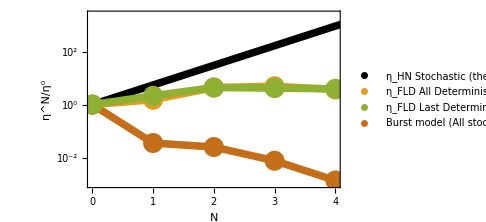

```mathematica
FigS2A=Legended[
Show[ListLogPlot[Table[{Ns,ηN/η0}/.xgParams/.testpoint,{Ns,0,4,1}],Frame->{{True,False},{True,False}},FrameLabel->{"N","η^N/η^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{PointSize[0.00],Black},FrameTicks->{{yticks,None},{{0,1,2,3,4},None}},PlotRange->{Automatic,{0.001,2500}}],
p2,
ListLogPlot[AllDetFLD,PlotStyle->{cmap[[2]],PointSize[0.04]}],
ListLogPlot[AllDetFLD,Joined->True,PlotStyle->{cmap[[2]],Thickness[0.015]}],

(*ListLogPlot[AllDetHN,PlotStyle->{cmap[[4]],PointSize[0.04]}],
ListLogPlot[AllDetHN,Joined->True,PlotStyle->{cmap[[4]],Thickness[0.015]}],*)

ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,PlotStyle->{cmap[[3]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015]}],


ListLogPlot[KPRGFLD1,PlotStyle->{cmap[[6]],PointSize[0.04]}],
ListLogPlot[KPRGFLD1,Joined->True,PlotStyle->{cmap[[6]],Thickness[0.015]}],

ImageSize->Medium
],
PointLegend[{Black,(*cmap[[4]],*)cmap[[2]],cmap[[3]],cmap[[6]]},{"η_HN Stochastic (theory)",(*"η_HN Determinstic (sim)",*)"η_FLD All Deterministic","η_FLD Last Deterministic","Burst model (All stochastic)"},LegendMarkerSize->25]]
```

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["FigS2A.pdf",FigS2A];
```

#### Plot ROC or other classification statistic

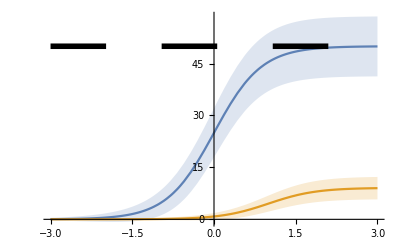

```mathematica
curves={
μ1/.koff->δ koff/.xgParams/.gtest->1,
(μ1+√Σ1)/.koff->δ koff/.xgParams/.gtest->1,
(μ1-√Σ1)/.koff->δ koff/.xgParams/.gtest->1,
μ1/.xgParams/.gtest->1,
(μ1+√Σ1)/.xgParams/.gtest->1,
(μ1-√Σ1)/.xgParams/.gtest->1
};
Show[
Plot[Evaluate@curves,{ctest,-3,3},PlotStyle->{cmap[[1]],None,None,cmap[[2]],None,None},Filling->{1->{2},1->{3},4->{5},4->{6}}],
Plot[Evaluate[μ1/.koff->δ koff/.xgParams/.gtest->1/.ctest->6],{ctest,-3,3},PlotStyle->{Black,Thickness[0.01],Dashing[0.1]}]
]
```

```mathematica
ROC[μ_,σ_,dth_:0.5,maxn_:500,ω_:10]:=Module[{TPR,FPR},
FPR=1-CDF[NormalDistribution[μ/.c->ω c,σ/.c->ω c],th];
TPR=1-CDF[NormalDistribution[μ/.koff->δ koff,σ/.koff->δ koff],th];
Table[{100FPR,100TPR},{th,0,maxn,dth}]
]

AUR[μ_,σ_,params_,dth_:0.5,maxn_:500,ω_:1]:=Module[{ROCcurve,data},
ROCcurve=ROC[μ,σ,dth,maxn,ω];
ROCcurve=ROCcurve/.params;
data=DeleteDuplicatesBy[ROCcurve,First];
data=DeleteDuplicatesBy[data,Last];
Integrate[Interpolation[data][x],{x,0,100}]/100^2
]
```

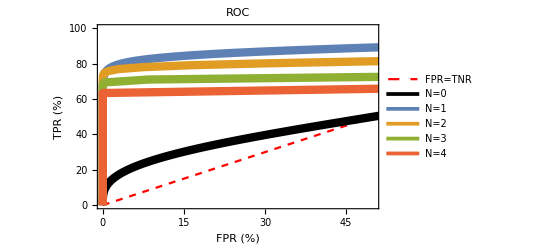

```mathematica
ROCparams={kon->1,kp->1,t->100,koff->1,δ->0.1,c->10^ctest,kf->10^-gtest};
testpoint={ctest->-1,gtest->1};

curves={Table[{i,i},{i,0,100}],
ROC[μ0,√Σ0,0.5,500,10]/.(ROCparams/.testpoint),
ROC[μ1,√Σ1,0.5,500,10]/.(ROCparams/.testpoint),
ROC[μ2,√Σ2,0.5,500,10]/.(ROCparams/.testpoint),
ROC[μ3,√Σ3,0.5,1000,10]/.(ROCparams/.testpoint),
ROC[μ4,√Σ4,0.5,1000,10]/.(ROCparams/.testpoint)
(*ROC[μN,ΣN]/.Ns->5/.expandParams/.ROCparams/.testpoint,
ROC[μN,ΣN]/.Ns->6/.expandParams/.ROCparams/.testpoint*)};

FigS2A=ListPlot[Evaluate@curves,
Joined->True,
PlotStyle->Join[{{Red,Dashed},{Black,Thickness[0.015]}},Table[{cmap[[i]],Thickness[0.015]},{i,1,Length[curves]-2}]],
PlotLabel->"ROC",
Frame->{{True,False},{True,False}},
FrameLabel->{"FPR (%)","TPR (%)"},
PlotLegends->Join[{"FPR=TNR"},Table[StringJoin["N=",ToString[i]],{i,0,Length[curves]-1}]],
PlotRange->{{0,50},{0,100}},
FrameStyle->Black,
LabelStyle->{Black,FontSize->16}
]
```

```mathematica
GMIN=-2;
GMAX=1.5;
ΔG=0.25;
tp={kon->1,kp->1,t->100,koff->1,δ->0.1,c->10^-1,kf->10^-GTEST};
AUCcurves={
Table[{GTEST,AUR[μ0,√Σ0,tp,0.5, Evaluate@5μ0/.tp/.GTEST->GMIN,10]},{GTEST,GMIN,GMAX,ΔG}],
Table[{GTEST,AUR[μ1,√Σ1,tp,0.01,Evaluate@5μ1/.tp/.GTEST->GMIN,10]},{GTEST,GMIN,GMAX,ΔG}],
Table[{GTEST,AUR[μ2,√Σ2,tp,0.005,Evaluate@5μ2/.tp/.GTEST->GMIN,10]},{GTEST,GMIN,GMAX,ΔG}],
Table[{GTEST,AUR[μ3,√Σ3,tp,0.002,Evaluate@5μ3/.tp/.GTEST->GMIN,10]},{GTEST,GMIN,GMAX,ΔG}],
Table[{GTEST,AUR[μ4,√Σ4,tp,0.005,Evaluate@5μ4/.tp/.GTEST->GMIN,10]},{GTEST,GMIN,GMAX,ΔG}](*,
Table[{GTEST,AUR[μN/.Ns->5/.expandParams,√ΣN/.Ns->5/.expandParams,tp,0.005,Evaluate@5μN/.Ns->5/.expandParams/.tp/.GTEST->GMIN,10]},{GTEST,GMIN,GMAX,ΔG}]*)
};
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 100 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

```mathematica
Table[{GTEST,AUR[μ0,√Σ0,tp,0.01,Evaluate@5μ0/.tp/.GTEST->GMIN,10]},{GTEST,GMIN,GMAX,ΔG}]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 100 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

{{-2.,0.48472},{-1.75,0.48472},{-1.5,0.48472},{-1.25,0.48472},{-1.,0.48472},{-0.75,0.48472},{-0.5,0.48472},{-0.25,0.48472},{0.,0.48472},{0.25,0.48472},{0.5,0.48472},{0.75,0.48472},{1.,0.48472},{1.25,0.48472},{1.5,0.48472}}

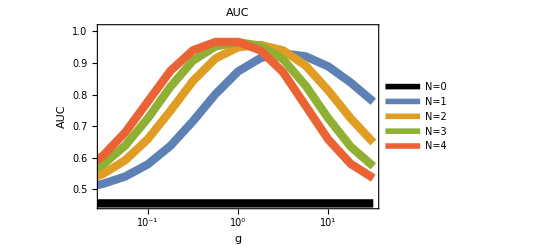

```mathematica
FigS2B=ListPlot[Evaluate@AUCcurves,
Joined->True,
PlotStyle->Join[{{Black,Thickness[0.015]}},Table[{cmap[[i]],Thickness[0.015]},{i,1,Length[curves]-1}]],
PlotLabel->"AUC",
Frame->{{True,False},{True,False}},
FrameLabel->{"g","AUC"},
PlotLegends->Table[StringJoin["N=",ToString[i]],{i,0,Length[AUCcurves]}],
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Table[{i,Superscript[10,i]},{i,Round[GMIN],Round[GMAX]}],None}},
LabelStyle->{Black,FontSize->16},
PlotRange->{{-1.5,GMAX},{0.45,1.01}}]
```

```mathematica
Evaluate@AUCcurves[[1]]
```

{{-2.,0.5},{-1.75,0.5},{-1.5,0.5},{-1.25,0.5},{-1.,0.5},{-0.75,0.5},{-0.5,0.5},{-0.25,0.5},{0.,0.5},{0.25,0.5},{0.5,0.5},{0.75,0.5},{1.,0.5},{1.25,0.5},{1.5,0.5}}

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

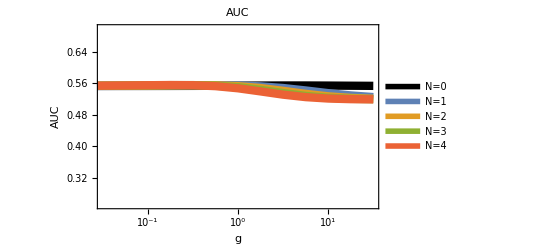

```mathematica
GMIN=-2;
GMAX=1.5;
ΔG=0.25;
tp={kon->1,kp->1,t->100,koff->1,δ->0.1,c->10^-1,kf->10^-GTEST};
AUCcurves={
Table[{GTEST,AUR[μ0,Σ0,tp,0.01,Evaluate@5μ1/.tp/.GTEST->GMIN]},{GTEST,GMIN,GMAX,ΔG}],
Table[{GTEST,AUR[μ1,Σ1,tp,0.01,Evaluate@5μ1/.tp/.GTEST->GMIN]},{GTEST,GMIN,GMAX,ΔG}],Table[{GTEST,AUR[μ2,Σ2,tp,0.005,Evaluate@5μ2/.tp/.GTEST->GMIN]},{GTEST,GMIN,GMAX,ΔG}],
Table[{GTEST,AUR[μ3,Σ3,tp,0.002,Evaluate@5μ3/.tp/.GTEST->GMIN]},{GTEST,GMIN,GMAX,ΔG}],
Table[{GTEST,AUR[μ4,Σ4,tp,0.005,Evaluate@5μ4/.tp/.GTEST->GMIN]},{GTEST,GMIN,GMAX,ΔG}]
};

ListPlot[Evaluate@AUCcurves,
Joined->True,
PlotStyle->Join[{{Black,Thickness[0.015]}},Table[{cmap[[i]],Thickness[0.015]},{i,1,Length[curves]-1}]],
PlotLabel->"AUC",
Frame->{{True,False},{True,False}},
FrameLabel->{"g","AUC"},
PlotLegends->Table[StringJoin["N=",ToString[i]],{i,0,Length[AUCcurves]}],
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Table[{i,Superscript[10,i]},{i,Round[GMIN],Round[GMAX]}],None}},
LabelStyle->{Black,FontSize->16},
PlotRange->{{-1.5,GMAX},{0.25,0.70}}]
```

```mathematica
GMIN=-2;
GMAX=1.5;
ΔG=0.25;
tp={kon->1,kp->1,t->100,koff->1,δ->0.1,c->10^1,kf->10^-GTEST};
AUCcurves={
Table[{GTEST,AUR[μ0,Σ0,tp,0.01,Evaluate@5μ1/.tp/.GTEST->GMIN]},{GTEST,GMIN,GMAX,ΔG}],
Table[{GTEST,AUR[μ1,Σ1,tp,0.01,Evaluate@5μ1/.tp/.GTEST->GMIN]},{GTEST,GMIN,GMAX,ΔG}],Table[{GTEST,AUR[μ2,Σ2,tp,0.005,Evaluate@5μ2/.tp/.GTEST->GMIN]},{GTEST,GMIN,GMAX,ΔG}],
Table[{GTEST,AUR[μ3,Σ3,tp,0.002,Evaluate@5μ3/.tp/.GTEST->GMIN]},{GTEST,GMIN,GMAX,ΔG}],
Table[{GTEST,AUR[μ4,Σ4,tp,0.005,Evaluate@5μ4/.tp/.GTEST->GMIN]},{GTEST,GMIN,GMAX,ΔG}]
};
```

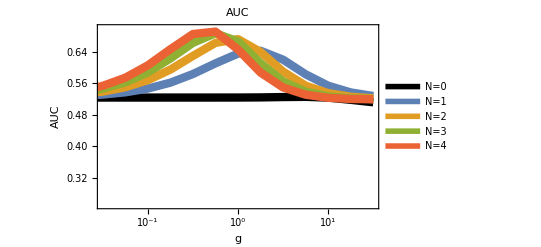

```mathematica
ListPlot[Evaluate@AUCcurves,
Joined->True,
PlotStyle->Join[{{Black,Thickness[0.015]}},Table[{cmap[[i]],Thickness[0.015]},{i,1,Length[AUCcurves]-1}]],
PlotLabel->"AUC",
Frame->{{True,False},{True,False}},
FrameLabel->{"g","AUC"},
PlotLegends->Table[StringJoin["N=",ToString[i]],{i,0,Length[AUCcurves]}],
FrameStyle->Black,
FrameTicks->{{Automatic,None},{Table[{i,Superscript[10,i]},{i,Round[GMIN],Round[GMAX]}],None}},
LabelStyle->{Black,FontSize->16},
PlotRange->{{-1.5,GMAX},{0.25,0.70}}]
```

#### Plot the FNR as a function of N, g

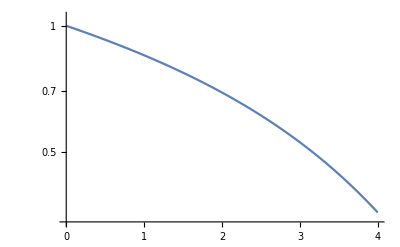

```mathematica
TH=μ0/.{koff->δ koff}/.(ROCparams/.testpoint);
LogPlot[(1-CDF[NormalDistribution[μN,ΣN],50])/(1-CDF[NormalDistribution[μ0,Σ0],50])/.expandParams/.(ROCparams/.testpoint),{Ns,0,4},PlotRange->All]
```

#### Wrongful activations amongst all activations

```mathematica
(*μ/.c->ω c/.params*)
```

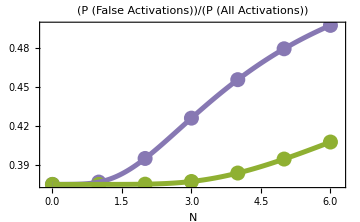

```mathematica
testparams={kon->1,kp->1,t->100,koff->1,δ->0.1,c->1,kf->0.1};
testparams2={kon->1,kp->1,t->100,koff->1,δ->0.1,c->1,kf->0.3};
FPoAp[μ_,σ_,params_,ω_:10]:=Module[{th=InverseCDF[NormalDistribution[μ/.c->ω c/.params,σ/.c->ω c/.params],0.40]},
((1-CDF[NormalDistribution[μ/.c->ω c,σ/.c->ω c],th])/((1-CDF[NormalDistribution[μ/.c->ω c,σ/.c->ω c],th])+(1-CDF[NormalDistribution[μ/.koff->δ koff,σ/.koff->δ koff],th]))/.params)
]
Fig4B=Show[
ListPlot[
{Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams,1]},{Ns,0,6}],
Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams2,1]},{Ns,0,6}]
},
Joined->False,
PlotRange->{{-0.15,6.2},Automatic},
PlotLabel->"(P (False Activations))/(P (All Activations))",
Frame->{{True,False},{True,False}},
FrameLabel->{"N",None},
FrameStyle->Black,
LabelStyle->{Black,FontSize->16},
PlotStyle->{{cmap[[5]],PointSize[0.03]},{cmap[[3]],PointSize[0.03]}},
ImageSize->Medium],
ListPlot[
{Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams,1]},{Ns,0,6,0.05}],
Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams2,1]},{Ns,0,6,0.05}]
},

Joined->True,
PlotStyle->{{cmap[[5]],Thickness[0.01]},{cmap[[3]],Thickness[0.01]}},
ImageSize->Medium]
]
```

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["Fig4B.pdf",Fig4B];
```

For external defense, have figures with different activation threshold:

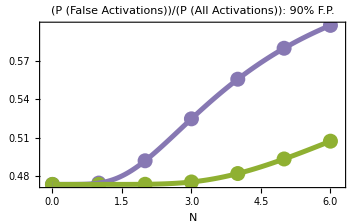

```mathematica
testparams={kon->1,kp->1,t->100,koff->1,δ->0.1,c->1,kf->0.1};
testparams2={kon->1,kp->1,t->100,koff->1,δ->0.1,c->1,kf->0.3};
FPoAp[μ_,σ_,params_,ω_:10]:=Module[{th=InverseCDF[NormalDistribution[μ/.c->ω c/.params,σ/.c->ω c/.params],0.10]},
((1-CDF[NormalDistribution[μ/.c->ω c,σ/.c->ω c],th])/((1-CDF[NormalDistribution[μ/.c->ω c,σ/.c->ω c],th])+(1-CDF[NormalDistribution[μ/.koff->δ koff,σ/.koff->δ koff],th]))/.params)
]
Show[
ListPlot[
{Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams,1]},{Ns,0,6}],
Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams2,1]},{Ns,0,6}]
},
Joined->False,
PlotRange->{{-0.15,6.2},Automatic},
PlotLabel->"(P (False Activations))/(P (All Activations)): 90% F.P.",
Frame->{{True,False},{True,False}},
FrameLabel->{"N",None},
FrameStyle->Black,
LabelStyle->{Black,FontSize->16},
PlotStyle->{{cmap[[5]],PointSize[0.03]},{cmap[[3]],PointSize[0.03]}},
ImageSize->Medium],
ListPlot[
{Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams,1]},{Ns,0,6,0.05}],
Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams2,1]},{Ns,0,6,0.05}]
},

Joined->True,
PlotStyle->{{cmap[[5]],Thickness[0.01]},{cmap[[3]],Thickness[0.01]}},
ImageSize->Medium]
]
```

#### Try non-exponential waiting time and deterministic burst of signal output

Choose the rate k_x of arrival in the final state (which is the second of two hidden states in the ‘final state’ of the previous KPR model) and the rate k_y of exit from this final state so that k_x=k_y and 1/k_x+1/k_y=1/k_off. This means k_x=k_y=2 k_off.

```mathematica
M1x={{-kon c,koff,0,kx},{kon c,-koff-kf,0,0},{0,kf,-kx,0},{0,0,kx,-kx}};
Pss1x={P0,P1,P2,P3}/.(Solve[Join[Table[(M1x.{P0,P1,P2,P3})[[i]]==0,{i,1,3}],{P0+P1+P2+P3==1}],{P0,P1,P2,P3}][[1]]);

M2x={{-kon c,koff,0,0,3koff},{kon c,-koff-kf,0,0,0},{0,kf,-3 koff,0,0},{0,0,3 koff,-3 koff, 0},{0,0,0,3koff,-3koff}};
Pss2x={P0,P1,P2,P3,P4}/.(Solve[Join[Table[(M2x.{P0,P1,P2,P3,P4})[[i]]==0,{i,1,4}],{P0+P1+P2+P3+P4==1}],{P0,P1,P2,P3,P4}][[1]]);
```

Mean signal ⟨n⟩:

⟨ṅ⟩=Σ_n Σ_i n((Ṗ)^n)_i
     =Σ_n n(-k_onc P_0^n+k_off P_1^n+k_off P_3^n
+k_on c P_0^n-k_off P_1^n-k_f P_1^n
+k_f P_1^(n-β)-k_x P_2^n
+k_x P_2^n-k_off P_3^n)
     =Σ_n n(k_f P_1^(n-β)-k_f P_1^n)
     =Σ_(n+β)(n+β) k_f P_1^n-Σ_n n k_f P_1^n
     =β k_f P_1

Variance in signal:
⟨ṅ⟩=Σ_n Σ_i n^2((Ṗ)^n)_i
    =Σ_n n^2(k_f P_1^(n-β)-k_f P_1^n)
    =k_f Σ_n((n+β)^2 P_1^n-n^2 k_f P_1^n)
    =k_f Σ_n((n^2+2nβ+β^2)P_1^n-n^2 k_f P_1^n)
    =k_f Σ_n(2nβ+β^2)P_1^n
    =k_f 2β ⟨n_1⟩+k_f β^2 P_1^ss
    
    Set of ODEs for partial averages:
    ⟨OverDot[n_i]⟩=Σ_n n((Ṗ)^n)_i

```mathematica
xVariance[M_,Pss_,SignalAtExitFromIndex_,BurstSize_]:=Module[{ndims,kF,npartials,nEqs,nfVec,nSol,nSubMeans,dNSQUAREdt,NSQUARE,meanM,CovNN},
ndims=Length[M];
kF=M[[SignalAtExitFromIndex+1,SignalAtExitFromIndex]];
npartials=Table[Symbol["n"<>ToString[i]],{i,1,ndims}];
nfVec=Table[0,{i,1,ndims}];
nfVec[[SignalAtExitFromIndex+1]]=BurstSize *kF Pss[[SignalAtExitFromIndex]];

nEqs=Join[
Table[D[npartials[[i]][t],t]==M[[i]].Table[npartials[[i]][t],{i,1,ndims}]+nfVec[[i]],{i,1,ndims}],
Table[npartials[[i]][0]==0,{i,1,ndims}]];
Print[nEqs];
nSol=DSolve[nEqs,npartials,t];
Print["DONE nSol"];
nSubMeans=Table[Evaluate[npartials/.nSol[[1]]][[i,2]],{i,1,ndims}];

dNSQUAREdt=2 BurstSize kF nSubMeans[[SignalAtExitFromIndex]]+kF BurstSize^2 Pss[[SignalAtExitFromIndex]];
NSQUARE=Integrate[dNSQUAREdt,t] // Simplify ;
Print["DONE Integrate"];
meanM=BurstSize kF t Pss[[SignalAtExitFromIndex]];
CovNN=NSQUARE- meanM^2//Simplify;
CovNN
]
```

```mathematica
meanX1=kf β t Pss1x[[2]]
meanX2=kf β t Pss2x[[2]]
```

(c kf kon kx t β)/(2 c kf kon+kf kx+koff kx+c kon kx)

(c kf koff kon t β)/((kf+koff) (koff+c kon))

```mathematica
varX1=xVariance[M1x,Pss1x,2,β]
```

kf

{n1'[t]==-c kon n1[t]+koff n2[t]+kx n4[t],n2'[t]==c kon n1[t]+(-kf-koff) n2[t],n3'[t]==(c kf kon kx β)/(2 c kf kon+kf kx+koff kx+c kon kx)+kf n2[t]-kx n3[t],n4'[t]==kx n3[t]-kx n4[t],n1[0]==0,n2[0]==0,n3[0]==0,n4[0]==0}

$Aborted

#### Short time distribution

```mathematica
M0={{-kon c,koff},{kon c q, -koff+kp(s-1)}};
M1={{-kon c,koff,koff},{kon c,-koff-kf,0},{0,kf q,-koff+kp(s-1)}};
M2={{-kon c,koff,koff,koff},{kon c,-koff-kf,0,0},{0,kf,-koff-kf,0},{0,0,kf q,-koff+kp(s-1)}};
M3={{-kon c,koff,koff,koff,koff},{kon c,-koff-kf,0,0,0},{0,kf,-koff-kf,0,0},{0,0,kf,-koff-kf,0},{0,0,0,kf q,-koff+kp(s-1)}};
M4={{-kon c,koff,koff,koff,koff,koff},{kon c,-koff-kf,0,0,0,0},{0,kf,-koff-kf,0,0,0},{0,0,kf,-koff-kf,0,0},{0,0,0,kf,-koff-kf,0},{0,0,0,0,kf q,-koff+kp(s-1)}};
```

```mathematica
ShortTimeMean[M_]:=Module[{Pinit,Msimp},
Pinit=Table[0,{i,1,Length[M]}];
Pinit[[1]]=1;
Msimp=M/.{kon c->KONC};
Assuming[koff>0&&kon>0&&c>0&&kp>0&&kf>0&&s==1&&q==1&&Element[koff|KONC|kf|s|q|t,Reals],Total[D[MatrixExp[Msimp t].Pinit,s]]//Simplify]
]

ShortTimeVariance[M_,mean_]:=Module[{Pinit,Msimp},
Pinit=Table[0,{i,1,Length[M]}];
Pinit[[1]]=1;
Msimp=M/.{kon c->KONC};
Evaluate[mean+Assuming[koff>0&&kon>0&&c>0&&kp>0&&s==1&&q==1&&kf>0&&Element[koff|kon|c|kf|s|q|t,Reals],Simplify[Total[D[MatrixExp[Msimp t].Pinit,{s,2}]][[1]]-mean^2]]]//Simplify
]
```

```mathematica
meanN0=ShortTimeMean[M0]/.{√((koff+KONC)^2)->(koff+KONC)}
varN0=ShortTimeVariance[M0,meanN0]/.{√((koff+KONC)^2)->(koff+KONC)}
```

(ⅇ^(-(koff+KONC) t) KONC kp (1+ⅇ^((koff+KONC) t) (-1+koff t+KONC t)))/(koff+KONC)^2

(ⅇ^(-2 (koff+KONC) t) KONC kp (ⅇ^((koff+KONC) t) (koff+KONC)^2 (1+ⅇ^((koff+KONC) t) (-1+koff t+KONC t))+(kp (-2 ⅇ^(-1/2 (-2 koff-2 KONC) t) (koff^2-4 koff KONC+KONC^2)-KONC (koff+KONC) (1+ⅇ^((koff+KONC) t) (-1+koff t+KONC t))^2))/(√((koff+KONC)^2))))/(koff+KONC)^4

```mathematica
Assuming[x>0&&koff>0&&Element[koff|x,Reals],Simplify[meanN0/.t->1/koff/.{KONC->koff x,kf->koff/g}]]
Assuming[x>0&&koff>0&&Element[koff|x,Reals],Simplify[varN0/.t->1/koff/.{KONC->koff x,kf->koff/g}]]
```

(ⅇ^(-1-x) kp x (1+ⅇ^(1+x) x))/(koff (1+x)^2)

(ⅇ^(-2 (1+x)) kp x (-kp x (1+x)+ⅇ^(2+2 x) x (1+x) (-kp x^2+koff (1+x)^2)+ⅇ^(1+x) (koff (1+x)^3-2 kp (1-4 x+2 x^2+x^3))))/(koff^2 (1+x)^5)

```mathematica
meanN1=ShortTimeMean[M1]/.{√((koff+KONC)^2)->(koff+KONC)}//Simplify;
meanN1st=Assuming[x>0&&koff>0&&Element[koff|x,Reals],Simplify[meanN1/.t->1/koff/.{KONC->koff x,kf->koff/g}]]
```

(ⅇ^(-(1+g+g x)/g) kp x (-ⅇ^(1/g) (1+g)^2+ⅇ^x g^2 (1+x)^2+ⅇ^(1+1/g+x) (g-x-g^2 x+g x^2)))/((1+g)^2 koff (1+x)^2 (-1+g x))

```mathematica
Block[{Pinit,Msimp,D1,D2},
Pinit=Table[0,{i,1,Length[M1]}];
Pinit[[1]]=1;
Msimp=M1/.{kon c->KONC};
D1=Assuming[koff>0&&kon>0&&c>0&&kp>0&&s==1&&q==1&&kf>0&&Element[koff|kon|c|kf|s|q|t,Reals],
Simplify[
D[MatrixExp[Msimp t].Pinit,{s,1}]
]
];
D2=Assuming[koff>0&&kon>0&&c>0&&kp>0&&s==1&&q==1&&kf>0&&Element[koff|kon|c|kf|s|q|t,Reals],
Simplify[
Total[D[D1,{s,1}]]
]
];
varN1=Simplify[meanN1+D2-meanN1^2]
]
```

1/((kf+koff)^4 (kf-KONC)^2 (koff+KONC)^4)ⅇ^(-2 (kf+koff+KONC) t) kf KONC kp (ⅇ^(kf t) (kf+koff)^2-ⅇ^(KONC t) (koff+KONC)^2+ⅇ^((kf+koff+KONC) t) (kf-KONC) (-KONC+koff^2 t+koff (-2+KONC t)+kf (-1+koff t+KONC t))) (ⅇ^((kf+koff+KONC) t) (kf+koff)^2 (kf-KONC) (koff+KONC)^2-kf KONC kp (ⅇ^(kf t) (kf+koff)^2-ⅇ^(KONC t) (koff+KONC)^2+ⅇ^((kf+koff+KONC) t) (kf-KONC) (-KONC+koff^2 t+koff (-2+KONC t)+kf (-1+koff t+KONC t))))

```mathematica
varN1st=Assuming[x>0&&koff>0&&Element[koff|x,Reals],Simplify[varN1/.t->1/koff/.{KONC->koff x,kf->koff/g}]]
```

-(ⅇ^(-2 (1+1/g+x)) kp x (ⅇ^(1/g) (1+g)^2 kp x-ⅇ^x g^2 kp x (1+x)^2+ⅇ^(1+1/g+x) (-1+g x) (kp (g-x) x+(1+g)^2 koff (1+x)^2)) (ⅇ^(1/g) (1+g)^2-ⅇ^x g^2 (1+x)^2+ⅇ^(1+1/g+x) (x+g^2 x-g (1+x^2))))/((1+g)^4 koff^2 (1+x)^4 (-1+g x)^2)

```mathematica
ShortTimeMean[M2]
```

Simplify::infd: Expression … simplified to Indeterminate.

Simplify::infd: Expression RootSum[-kf^2 koff KONC-kf^2 KONC kp+kf^2 koff KONC q+kf^2 KONC kp s-kf^2 koff #1-2 kf koff^2 #1-koff^3 #1-kf^2 KONC #1-2 kf koff KONC #1-koff^2 KONC #1-kf^2 kp #1-2 kf koff kp #1-koff^2 kp #1-2 kf KONC kp #1-koff KONC kp #1+kf^2 kp s #1+2 kf koff kp s #1+koff^2 kp s #1+2 kf KONC kp s #1+koff KONC kp s #1-kf^2 #1^2-4 kf koff #1^2-3 koff^2 #1^2-2 kf KONC #1^2-2 koff KONC #1^2-2 kf kp #1^2-2 koff kp #1^2-KONC kp #1^2+2 kf kp s #1^2+2 koff kp s #1^2+KONC kp s #1^2-2 kf #1^3-3 koff #1^3-KONC #1^3-kp #1^3+kp s #1^3-#1^4&,(«1»)/(kf^6 koff^3+6 kf^5 koff^4+«60»+17 kf^4 koff^2 KONC^2 kp+«1430»)&] simplified to Indeterminate.

Simplify::infd: Expression … simplified to Indeterminate.

General::stop: Further output of Simplify::infd will be suppressed during this calculation.

Indeterminate

```mathematica
Block[{Pinit,Msimp,D1,A},
Pinit=Table[0,{i,1,Length[M2]}];
Pinit[[1]]=1;
Msimp=M2/.{kon c->KONC,q->1};
A=(MatrixExp[Msimp t].Pinit)//Simplify;
Total[D[A,s]]//Simplify
]
(*
D1=Assuming[koff>0&&kon>0&&c>0&&kp>0&&kf>0&&Element[koff|kon|c|kf|t,Reals],
Simplify[
D[,s]
]
];
Total[D1]
]*)
```

$Aborted

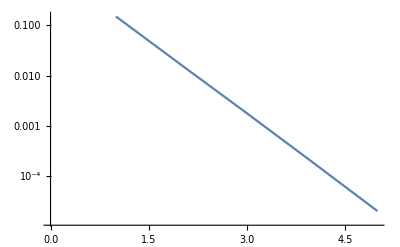

```mathematica
λ=kf/(s+kf+koff);
C1=1/(s+kf-koff((1-λ^Ns)/(1-λ)-1));
fs=kf C1 λ^(Ns-1);
CDFmfpt[T_,params_]:=Integrate[InverseLaplaceTransform[fs,s,t]/.params,{t,0,T}]

ListLogPlot[Table[(Re@CDFmfpt[0.1,{koff->10,kf->1,Ns->i}])/(Re@CDFmfpt[1,{koff->1,kf->1,Ns->i}]),{i,1,5}],Joined->True]
```

#### Short time estimation

The probability for one cycle of a non-proofreading receptor is given by:

p_0=e^(-k_onc(t_1-t_0))k_on c e^(-k_off(t_2-t_1))k_off  such that (t_1-t_0)+(t_2-t_1)=T   *Note that t_1-t_0=T_u and t_2-t_1=T_b  for T_u the total time spent unbound and T_b bound

For a proofreading receptor with N proofreading steps, the probability of one cycle in total time T' is:
p_N=e^(-k_onc(t_1-t_0))k_on c e^(-k_f(t_(N+1)-t_1))k_f^N e^(-k_off(t_(N+2)-t_(N+1)))k_off    for N≥1 and t_(N+1)-t_0=T'
      =e^(-k_on cT_u)k_on c e^(-k_f(T_b-τ))k_f^N e^-k_offτ k_off  where τ=(t_(N+2)-t_(N+1))

Maximizing the probability over k_off via dP/dk_off=0 gives the MLE for a single binding event.

For N=0 this is:
0=1/k_off p_0-T_b p_0 so the best estimate is k_off^*=T_b^-1
For N≥1 this is:
0=1/k_off p_N-τ p_0 so the best estimate is k_off^*=τ^-1

```mathematica
-1/(koff^2(D[Log[E^(-kon c Tu)kon c e^(-kf(Tb-τ))kf^Ns E^(-koff τ)koff],{koff,2}]/.koff->τ^-1))
```

1/(koff^2 τ^2)

```mathematica
D[E^(-kon c Tu)kon c e^(-kf(Tb-τ))kf^Ns E^(-koff τ)koff,{koff,2}]//Simplify
```

c e^(kf (-Tb+τ)) ⅇ^(-c kon Tu-koff τ) kf^Ns kon τ (-2+koff τ)

#### Short time validity

```mathematica
FLDReviewer2ModelSimLongTime500={{0,1.00},{1,22989.68},{2,16091.00},{3,6577.72},{4,2813.05}};

FLDReviewer2ModelSimShortTime50={{0,1.00},{1,0.97},{2,0.56},{3,0.26},{4,0.12}};
(*{{0,1.00},{1,1455.89},{2,1479.28},{3,656.58},{4,300.28}};*)(*G protein, β=1*)
(*{{0,1.00},{1,2640.67},{2,2825.06},{3,1428.18},{4,619.68}};*)(*Burst size 10*)

FLDReviewer2ModelSimShortTime5={{0,1.00},{1,0.99},{2,0.58},{3,0.24},{4,0.09}};
(*{{0,1.00},{1,8.59},{2,5.33},{3,2.09},{4,0.79}};*)(*G protein, β=1*)
(*{{0,1.00},{1,161.42},{2,88.62},{3,47.10},{4,16.64}};*)(*Burst size 10*)

FLDReviewer2ModelSimShortTime05={{0,1.00},{1,0.92},{2,0.32},{3,0.05},{4,0.02}};
(*{{0,1.00},{1,189.44},{2,70.33},{3,21.23},{4,3.25}};*)(*G protein, β=1*)
(*{{0,1.00},{1,135.41},{2,59.19},{3,25.22},{4,3.58}}*)(*Burst size 10*)
combined={FLDReviewer2ModelSimShortTime05,FLDReviewer2ModelSimShortTime5,FLDReviewer2ModelSimShortTime50};

FLDtheory={{0,1},{1,KPR1BPn/KPR0BPn},{2,KPR2BPn/KPR0BPn},{3,KPR3BPn/KPR0BPn},{4,KPR4BPn/KPR0BPn}}/.xgParams/.{ctest->1,gtest->1};
```

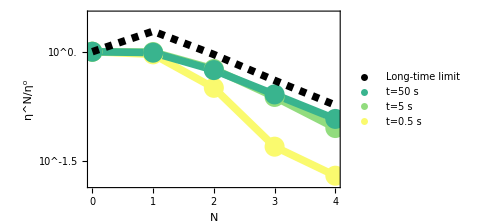

```mathematica
FigS3E=Show[
Legended[ListLogPlot[combined,
Joined->True,
PlotStyle->Table[{Thickness[0.015],gradcolor[[i]]},{i,1,7,2}],
Frame->{{True,False},{True,False}},

FrameLabel->{"N","η^N/η^0"},
FrameStyle->Black,
FrameTicksStyle->{Black,FontSize->16},
LabelStyle->{Black,FontSize->16},

FrameTicks->{{Table[{2.3i,Superscript[10,i]},{i,-3,4,0.5}],None},{{0,1,2,3,4},None}},
PlotRange->{Automatic,{Automatic,10^0.51}},
ImageSize->Medium],
PointLegend[Join[{Black},Table[gradcolor[[i]],{i,5,1,-2}]],{"Long-time limit","t=50 s","t=5 s","t=0.5 s"},LegendMarkerSize->25]],
ListLogPlot[combined,PlotStyle->Table[{PointSize[0.04],gradcolor[[i]]},{i,1,7,2}]],
ListLogPlot[FLDtheory,Joined->True,PlotStyle->{Black,Thickness[0.015],Dashed}]
]
```

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
Export["FigS3E.pdf",FigS3E];
```